```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

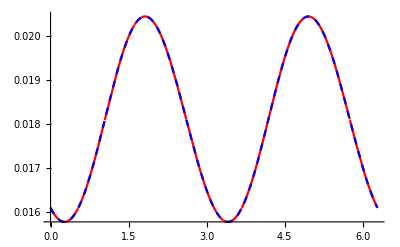

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

```mathematica
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-Graphics-
```

0

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

-Graphics-

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

-Graphics-

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

## b=0.2 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,i,kT,x1u,x3u,bu},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
Print["b=",b, ", θA=",θA,", θB=",θB];
v2kTb05
]
```

```mathematica
showdσHZ[{1.0,0},{0.5,0.5},{1.0,0},1.0,False]
```

{-0.0908371,-0.224816}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13331140 near {ϕ$13331140} = {0.944835}. NIntegrate obtained 3.03577×10^-18 and 1.59815×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13381593 near {ϕ$13381593} = {2.19656}. NIntegrate obtained -6.90795×10^-14 and 2.01972×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13433313 near {ϕ$13433313} = {0.957106}. NIntegrate obtained 4.10215×10^-13 and 1.85111×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

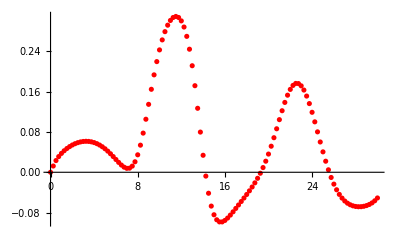

b=0.2, θA=0, θB=π/2

{{0.,{0.,0.}},{0.25,{0.0124114,2.80576×10^-16}},{0.5,{0.0232611,-4.08377×10^-12}},{0.75,{0.031172,1.85383×10^-11}},{1.,{0.0374765,-2.49941×10^-12}},{1.25,{0.0427321,-2.40734×10^-12}},{1.5,{0.0471895,1.75373×10^-12}},{1.75,{0.0509731,-5.97151×10^-14}},{2.,{0.0541471,1.51111×10^-10}},{2.25,{0.0567448,-2.0182×10^-12}},{2.5,{0.0587807,1.49059×10^-9}},{2.75,{0.0602582,-3.86329×10^-13}},{3.,{0.0611725,-7.48825×10^-13}},{3.25,{0.0615135,2.31142×10^-10}},{3.5,{0.0612673,-2.82087×10^-11}},{3.75,{0.0604176,1.42307×10^-11}},{4.,{0.0589473,-5.18141×10^-12}},{4.25,{0.0568407,9.87835×10^-11}},{4.5,{0.0540861,3.57604×10^-9}},{4.75,{0.0506804,3.65006×10^-18}},{5.,{0.0466349,-5.22748×10^-11}},{5.25,{0.041984,2.447×10^-12}},{5.5,{0.036797,3.8448×10^-11}},{5.75,{0.0311951,7.3019×10^-11}},{6.,{0.0253723,-1.92226×10^-9}},{6.25,{0.0196225,-9.95017×10^-9}},{6.5,{0.0143682,-3.38954×10^-12}},{6.75,{0.0101878,5.57133×10^-10}},{7.,{0.00782756,-7.40362×10^-10}},{7.25,{0.0081825,-3.94911×10^-9}},{7.5,{0.0122224,1.98121×10^-12}},{7.75,{0.0208471,9.92332×10^-12}},{8.,{0.0346762,-1.83302×10^-12}},{8.25,{0.0538272,-2.21981×10^-12}},{8.5,{0.0777663,-2.27283×10^-7}},{8.75,{0.105325,5.53151×10^-10}},{9.,{0.134901,-4.48933×10^-10}},{9.25,{0.164781,-6.30528×10^-10}},{9.5,{0.193445,-9.69129×10^-10}},{9.75,{0.219759,4.07097×10^-9}},{10.,{0.243018,-1.64605×10^-9}},{10.25,{0.262877,4.45615×10^-10}},{10.5,{0.279233,1.20397×10^-10}},{10.75,{0.292096,4.64349×10^-11}},{11.,{0.301481,-5.38846×10^-10}},{11.25,{0.307323,-1.20537×10^-9}},{11.5,{0.309416,4.20317×10^-10}},{11.75,{0.307377,2.06708×10^-11}},{12.,{0.300623,4.98141×10^-10}},{12.25,{0.288409,-5.20705×10^-10}},{12.5,{0.269905,-1.23303×10^-9}},{12.75,{0.244392,8.54087×10^-10}},{13.,{0.211564,-1.00727×10^-10}},{13.25,{0.171911,-1.2567×10^-9}},{13.5,{0.127057,-4.26052×10^-8}},{13.75,{0.0798133,4.22581×10^-9}},{14.,{0.0337525,-1.60746×10^-9}},{14.25,{-0.00759671,2.1944×10^-9}},{14.5,{-0.0416341,-1.69299×10^-8}},{14.75,{-0.0671704,-4.77504×10^-9}},{15.,{-0.0843707,6.01765×10^-8}},{15.25,{-0.094327,-4.83163×10^-7}},{15.5,{-0.0985451,-1.99271×10^-9}},{15.75,{-0.0985482,4.38024×10^-8}},{16.,{-0.0956487,-2.5549×10^-10}},{16.25,{-0.0908858,4.96037×10^-9}},{16.5,{-0.0850093,-5.87865×10^-10}},{16.75,{-0.0785323,4.1338×10^-10}},{17.,{-0.0717785,1.76295×10^-10}},{17.25,{-0.0649301,-7.97831×10^-11}},{17.5,{-0.0580556,5.2949×10^-8}},{17.75,{-0.0511468,-4.25117×10^-9}},{18.,{-0.0441306,-1.75729×10^-9}},{18.25,{-0.0368829,-5.21132×10^-9}},{18.5,{-0.0292413,-1.87489×10^-8}},{18.75,{-0.021014,2.56137×10^-8}},{19.,{-0.0119862,-2.68908×10^-8}},{19.25,{-0.00193804,-1.04826×10^-9}},{19.5,{0.00933448,-9.1959×10^-9}},{19.75,{0.0220012,9.81292×10^-10}},{20.,{0.0361472,-6.50141×10^-10}},{20.25,{0.0517458,-8.76004×10^-8}},{20.5,{0.0686145,-4.18991×10^-9}},{20.75,{0.0863851,9.86208×10^-10}},{21.,{0.104498,-2.13047×10^-9}},{21.25,{0.12222,7.46952×10^-10}},{21.5,{0.138708,1.84264×10^-10}},{21.75,{0.15309,1.5221×10^-9}},{22.,{0.164564,7.1916×10^-9}},{22.25,{0.172479,-7.08722×10^-10}},{22.5,{0.176398,-5.48817×10^-9}},{22.75,{0.176119,-8.84896×10^-9}},{23.,{0.171666,8.84524×10^-8}},{23.25,{0.16327,-9.34355×10^-10}},{23.5,{0.151339,3.01382×10^-10}},{23.75,{0.136404,-2.41435×10^-9}},{24.,{0.119105,-1.20745×10^-7}},{24.25,{0.100147,7.52188×10^-10}},{24.5,{0.0802502,8.44855×10^-9}},{24.75,{0.0601565,1.13119×10^-7}},{25.,{0.0405337,9.49174×10^-8}},{25.25,{0.0219649,-5.17974×10^-8}},{25.5,{0.00490753,5.06116×10^-9}},{25.75,{-0.0103202,-3.26835×10^-9}},{26.,{-0.0235443,1.93578×10^-7}},{26.25,{-0.034726,3.80914×10^-9}},{26.5,{-0.0439346,4.19617×10^-9}},{26.75,{-0.0513115,-3.07593×10^-9}},{27.,{-0.0570638,3.10088×10^-9}},{27.25,{-0.0613924,3.69027×10^-8}},{27.5,{-0.064521,-7.31324×10^-8}},{27.75,{-0.0666372,3.29892×10^-10}},{28.,{-0.0679016,2.84138×10^-9}},{28.25,{-0.0684354,-2.21716×10^-9}},{28.5,{-0.0683109,-4.02316×10^-8}},{28.75,{-0.0675485,-4.42421×10^-9}},{29.,{-0.0661185,1.15825×10^-8}},{29.25,{-0.0639291,9.93665×10^-9}},{29.5,{-0.0608324,-1.38388×10^-9}},{29.75,{-0.0566195,3.15058×10^-9}},{30.,{-0.0510219,1.46714×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22908186 near {ϕ$22908186} = {0.503048}. NIntegrate obtained -4.46282×10^-6 and 1.34687×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23502992 near {ϕ$23502992} = {3.43602}. NIntegrate obtained -7.2388×10^-6 and 1.68782×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23586808 near {ϕ$23586808} = {1.98794}. NIntegrate obtained 1.11828×10^-6 and 2.81974×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

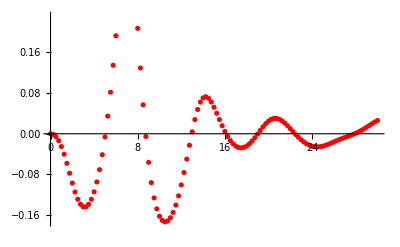

b=0.2, θA=π/4, θB=π/2

{{0.,{0.,0.}},{0.25,{-0.00138757,0.00111192}},{0.5,{-0.00578745,0.00483612}},{0.75,{-0.013612,0.0119627}},{1.,{-0.0251177,0.0232925}},{1.25,{-0.0401649,0.0393329}},{1.5,{-0.0580542,0.0600221}},{1.75,{-0.0775139,0.0845725}},{2.,{-0.0968807,0.111531}},{2.25,{-0.114421,0.139055}},{2.5,{-0.128654,0.165299}},{2.75,{-0.138555,0.188731}},{3.,{-0.14358,0.208296}},{3.25,{-0.143562,0.223408}},{3.5,{-0.138561,0.233836}},{3.75,{-0.128711,0.239569}},{4.,{-0.114113,0.240685}},{4.25,{-0.0947679,0.237262}},{4.5,{-0.0705402,0.229324}},{4.75,{-0.04116,0.21682}},{5.,{-0.00625251,0.199631}},{5.25,{0.034582,0.177628}},{5.5,{0.0816064,0.15077}},{5.75,{0.134649,0.119322}},{6.,{0.192607,0.0841842}},{6.25,{0.252718,0.047377}},{6.5,{0.309772,0.0125575}},{6.75,{0.355764,-0.0148097}},{7.,{0.381012,-0.0282595}},{7.25,{0.377396,-0.022564}},{7.5,{0.342613,0.00344774}},{7.75,{0.282203,0.0456583}},{8.,{0.207198,0.0963986}},{8.25,{0.129233,0.147787}},{8.5,{0.0568543,0.194165}},{8.75,{-0.00542725,0.232639}},{9.,{-0.056242,0.262418}},{9.25,{-0.0960323,0.283895}},{9.5,{-0.126018,0.297949}},{9.75,{-0.147582,0.305532}},{10.,{-0.161985,0.307498}},{10.25,{-0.170252,0.304536}},{10.5,{-0.173161,0.297174}},{10.75,{-0.171272,0.285813}},{11.,{-0.164969,0.270768}},{11.25,{-0.154518,0.252329}},{11.5,{-0.140124,0.230822}},{11.75,{-0.122012,0.206684}},{12.,{-0.100515,0.180543}},{12.25,{-0.0761703,0.153295}},{12.5,{-0.0498135,0.126147}},{12.75,{-0.0226388,0.100598}},{13.,{0.00382255,0.0783251}},{13.25,{0.0278388,0.0609441}},{13.5,{0.0477311,0.0496998}},{13.75,{0.0621858,0.0451698}},{14.,{0.0705174,0.0471082}},{14.25,{0.0727788,0.0544971}},{14.5,{0.0696796,0.0657933}},{14.75,{0.0623636,0.0792524}},{15.,{0.0521453,0.093227}},{15.25,{0.040293,0.106357}},{15.5,{0.0278926,0.11764}},{15.75,{0.0157961,0.126426}},{16.,{0.00462605,0.132354}},{16.25,{-0.00519222,0.135285}},{16.5,{-0.0133839,0.135247}},{16.75,{-0.0197864,0.132385}},{17.,{-0.0243184,0.126932}},{17.25,{-0.0269573,0.119205}},{17.5,{-0.0277272,0.109593}},{17.75,{-0.0266952,0.0985715}},{18.,{-0.0239758,0.0867046}},{18.25,{-0.0197376,0.0746526}},{18.5,{-0.0142122,0.0631644}},{18.75,{-0.00770274,0.0530546}},{19.,{-0.000584394,0.0451598}},{19.25,{0.00670601,0.0402677}},{19.5,{0.0136945,0.0390312}},{19.75,{0.0199063,0.041874}},{20.,{0.0249164,0.0489147}},{20.25,{0.0283943,0.0599258}},{20.5,{0.030143,0.074346}},{20.75,{0.0301161,0.0913457}},{21.,{0.0284112,0.109931}},{21.25,{0.0252439,0.129058}},{21.5,{0.0209093,0.147744}},{21.75,{0.0157412,0.165143}},{22.,{0.0100758,0.180589}},{22.25,{0.0042272,0.193613}},{22.5,{-0.00153054,0.203936}},{22.75,{-0.00696763,0.211448}},{23.,{-0.0119023,0.216185}},{23.25,{-0.0161946,0.218321}},{23.5,{-0.0197461,0.218147}},{23.75,{-0.0224925,0.216065}},{24.,{-0.0244032,0.212587}},{24.25,{-0.0254796,0.208333}},{24.5,{-0.0257544,0.20401}},{24.75,{-0.0252921,0.200403}},{25.,{-0.0241882,0.198316}},{25.25,{-0.0225632,0.198519}},{25.5,{-0.0205578,0.201664}},{25.75,{-0.0183175,0.2082}},{26.,{-0.0159797,0.2183}},{26.25,{-0.0136553,0.231827}},{26.5,{-0.0114205,0.248345}},{26.75,{-0.00930362,0.26717}},{27.,{-0.00728952,0.287465}},{27.25,{-0.00532981,0.308347}},{27.5,{-0.00335073,0.328973}},{27.75,{-0.00126903,0.348611}},{28.,{0.000995414,0.366679}},{28.25,{0.0035074,0.382752}},{28.5,{0.00630546,0.396552}},{28.75,{0.00939617,0.407937}},{29.,{0.012744,0.416875}},{29.25,{0.0162653,0.423427}},{29.5,{0.0198179,0.427736}},{29.75,{0.0231966,0.430026}},{30.,{0.0261243,0.4306}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29968485 near {ϕ$29968485} = {3.87781}. NIntegrate obtained 1.53905×10^-14 and 2.97945×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30035375 near {ϕ$30035375} = {6.01778009555628290438988869937020353972911834716796875}. NIntegrate obtained 6.95694×10^-14 and 1.03014×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30139452 near {ϕ$30139452} = {5.71858}. NIntegrate obtained 2.65142×10^-13 and 1.0038×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

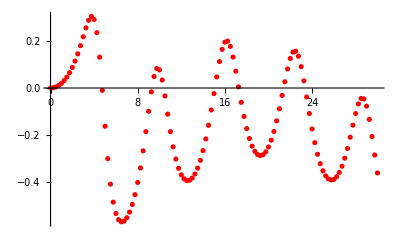

b=0.2, θA=π/2, θB=π/2

{{0.,{0.,0.}},{0.25,{0.00120005,5.87433×10^-16}},{0.5,{0.00484064,1.1378×10^-14}},{0.75,{0.0110282,1.07199×10^-13}},{1.,{0.0199274,2.54968×10^-15}},{1.25,{0.0317627,8.41268×10^-14}},{1.5,{0.0468171,1.74024×10^-13}},{1.75,{0.0654236,6.65305×10^-18}},{2.,{0.0879378,-1.04971×10^-12}},{2.25,{0.114674,-2.84788×10^-15}},{2.5,{0.14577,9.41824×10^-13}},{2.75,{0.18093,-2.39×10^-12}},{3.,{0.218953,-9.62304×10^-11}},{3.25,{0.256927,2.29637×10^-9}},{3.5,{0.289082,1.5685×10^-12}},{3.75,{0.305596,-6.56618×10^-17}},{4.,{0.29269,-5.8027×10^-9}},{4.25,{0.236452,1.11352×10^-11}},{4.5,{0.131609,-8.38321×10^-13}},{4.75,{-0.0102193,-4.43938×10^-12}},{5.,{-0.163272,7.34491×10^-11}},{5.25,{-0.301583,2.63769×10^-10}},{5.5,{-0.410447,4.24856×10^-11}},{5.75,{-0.487181,7.47374×10^-11}},{6.,{-0.535832,-1.49714×10^-11}},{6.25,{-0.562288,4.92507×10^-10}},{6.5,{-0.571781,1.14725×10^-7}},{6.75,{-0.568139,-8.58199×10^-11}},{7.,{-0.553792,3.80709×10^-12}},{7.25,{-0.530035,-2.58482×10^-11}},{7.5,{-0.497289,-6.71574×10^-11}},{7.75,{-0.455334,-4.22623×10^-11}},{8.,{-0.403555,1.01906×10^-11}},{8.25,{-0.341287,-1.26031×10^-10}},{8.5,{-0.268399,-1.12183×10^-9}},{8.75,{-0.186291,-8.49465×10^-11}},{9.,{-0.0993531,-1.2918×10^-9}},{9.25,{-0.0164173,-1.60128×10^-11}},{9.5,{0.0492215,-7.69317×10^-9}},{9.75,{0.0832938,-2.25993×10^-10}},{10.,{0.0773342,-1.64166×10^-10}},{10.25,{0.0340631,-1.29661×10^-9}},{10.5,{-0.0340215,1.26271×10^-8}},{10.75,{-0.111511,-5.3079×10^-10}},{11.,{-0.186194,1.6153×10^-11}},{11.25,{-0.251075,1.45082×10^-11}},{11.5,{-0.303415,1.17462×10^-10}},{11.75,{-0.342991,-6.53193×10^-11}},{12.,{-0.370704,4.75127×10^-12}},{12.25,{-0.387757,-5.45482×10^-11}},{12.5,{-0.395254,-3.81883×10^-10}},{12.75,{-0.394039,1.21225×10^-10}},{13.,{-0.384654,5.00907×10^-11}},{13.25,{-0.367356,-9.45436×10^-11}},{13.5,{-0.342159,-2.70804×10^-10}},{13.75,{-0.308901,-1.37342×10^-10}},{14.,{-0.267352,8.07746×10^-11}},{14.25,{-0.217385,5.09931×10^-8}},{14.5,{-0.159235,4.56522×10^-10}},{14.75,{-0.0939094,-4.57534×10^-10}},{15.,{-0.0236993,5.79058×10^-10}},{15.25,{0.0472688,4.70379×10^-10}},{15.5,{0.112768,4.97196×10^-10}},{15.75,{0.164949,1.41495×10^-9}},{16.,{0.19596,1.21005×10^-9}},{16.25,{0.200449,1.93136×10^-10}},{16.5,{0.177748,1.52422×10^-10}},{16.75,{0.132275,-3.02228×10^-10}},{17.,{0.0718378,-3.01646×10^-10}},{17.25,{0.00497991,2.24984×10^-8}},{17.5,{-0.0611226,-5.09428×10^-10}},{17.75,{-0.121542,2.77911×10^-8}},{18.,{-0.173491,-3.43288×10^-8}},{18.25,{-0.21576,-2.02523×10^-10}},{18.5,{-0.248106,4.42768×10^-9}},{18.75,{-0.270776,5.54283×10^-10}},{19.,{-0.284191,-6.1474×10^-10}},{19.25,{-0.288757,2.17543×10^-9}},{19.5,{-0.284779,1.2813×10^-9}},{19.75,{-0.272427,4.64154×10^-10}},{20.,{-0.251758,1.03915×10^-9}},{20.25,{-0.222782,7.31035×10^-10}},{20.5,{-0.18558,-3.26514×10^-8}},{20.75,{-0.140516,2.91041×10^-9}},{21.,{-0.088542,2.57527×10^-9}},{21.25,{-0.0316099,3.63799×10^-9}},{21.5,{0.0268718,4.61162×10^-9}},{21.75,{0.0817394,3.50222×10^-8}},{22.,{0.126278,-8.67207×10^-10}},{22.25,{0.153301,2.68949×10^-8}},{22.5,{0.157117,9.45149×10^-8}},{22.75,{0.135645,-2.49986×10^-9}},{23.,{0.0914338,4.35577×10^-10}},{23.25,{0.0307896,-7.582×10^-10}},{23.5,{-0.0383763,-5.55097×10^-9}},{23.75,{-0.108758,-8.43307×10^-9}},{24.,{-0.174923,2.82652×10^-8}},{24.25,{-0.23355,1.82978×10^-9}},{24.5,{-0.283036,1.54162×10^-8}},{24.75,{-0.322923,-2.24065×10^-9}},{25.,{-0.353388,-1.15135×10^-8}},{25.25,{-0.374873,5.81177×10^-10}},{25.5,{-0.38786,5.09261×10^-8}},{25.75,{-0.392742,-2.52093×10^-9}},{26.,{-0.389767,4.20277×10^-10}},{26.25,{-0.379024,2.53651×10^-9}},{26.5,{-0.360475,7.28979×10^-9}},{26.75,{-0.334035,1.78793×10^-10}},{27.,{-0.299735,1.21742×10^-8}},{27.25,{-0.257999,4.03857×10^-9}},{27.5,{-0.210099,7.70365×10^-9}},{27.75,{-0.158783,1.3498×10^-8}},{28.,{-0.108942,-1.10664×10^-7}},{28.25,{-0.0678878,1.68516×10^-8}},{28.5,{-0.0444845,1.15379×10^-8}},{28.75,{-0.0465873,7.26623×10^-9}},{29.,{-0.0775133,-1.92088×10^-8}},{29.25,{-0.133916,7.15144×10^-9}},{29.5,{-0.206969,1.18129×10^-8}},{29.75,{-0.286134,2.43145×10^-8}},{30.,{-0.362663,2.09513×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38759296 near {ϕ$38759296} = {5.79221}. NIntegrate obtained -4.46282×10^-6 and 1.34687×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39353355 near {ϕ$39353355} = {2.85924}. NIntegrate obtained -7.2388×10^-6 and 1.68782×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39437171 near {ϕ$39437171} = {4.30732}. NIntegrate obtained 1.11828×10^-6 and 2.81974×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

b=0.2, θA=(3 π)/4, θB=π/2

{{0.,{0.,0.}},{0.25,{-0.00138757,-0.00111192}},{0.5,{-0.00578745,-0.00483612}},{0.75,{-0.013612,-0.0119627}},{1.,{-0.0251177,-0.0232925}},{1.25,{-0.0401649,-0.0393329}},{1.5,{-0.0580542,-0.0600221}},{1.75,{-0.0775139,-0.0845725}},{2.,{-0.0968807,-0.111531}},{2.25,{-0.114421,-0.139055}},{2.5,{-0.128654,-0.165299}},{2.75,{-0.138555,-0.188731}},{3.,{-0.14358,-0.208296}},{3.25,{-0.143562,-0.223408}},{3.5,{-0.138561,-0.233836}},{3.75,{-0.128711,-0.239569}},{4.,{-0.114113,-0.240685}},{4.25,{-0.0947679,-0.237262}},{4.5,{-0.0705402,-0.229324}},{4.75,{-0.04116,-0.21682}},{5.,{-0.00625251,-0.199631}},{5.25,{0.034582,-0.177628}},{5.5,{0.0816064,-0.15077}},{5.75,{0.134649,-0.119322}},{6.,{0.192607,-0.0841842}},{6.25,{0.252718,-0.047377}},{6.5,{0.309772,-0.0125575}},{6.75,{0.355764,0.0148097}},{7.,{0.381012,0.0282595}},{7.25,{0.377396,0.022564}},{7.5,{0.342613,-0.00344774}},{7.75,{0.282203,-0.0456583}},{8.,{0.207198,-0.0963986}},{8.25,{0.129233,-0.147787}},{8.5,{0.0568543,-0.194165}},{8.75,{-0.00542725,-0.232639}},{9.,{-0.056242,-0.262418}},{9.25,{-0.0960323,-0.283895}},{9.5,{-0.126018,-0.297949}},{9.75,{-0.147582,-0.305532}},{10.,{-0.161985,-0.307498}},{10.25,{-0.170252,-0.304536}},{10.5,{-0.173161,-0.297174}},{10.75,{-0.171272,-0.285813}},{11.,{-0.164969,-0.270768}},{11.25,{-0.154518,-0.252329}},{11.5,{-0.140124,-0.230822}},{11.75,{-0.122012,-0.206684}},{12.,{-0.100515,-0.180543}},{12.25,{-0.0761703,-0.153295}},{12.5,{-0.0498135,-0.126147}},{12.75,{-0.0226388,-0.100598}},{13.,{0.00382255,-0.0783251}},{13.25,{0.0278388,-0.0609441}},{13.5,{0.0477311,-0.0496998}},{13.75,{0.0621858,-0.0451698}},{14.,{0.0705174,-0.0471082}},{14.25,{0.0727788,-0.0544971}},{14.5,{0.0696796,-0.0657933}},{14.75,{0.0623636,-0.0792524}},{15.,{0.0521453,-0.093227}},{15.25,{0.040293,-0.106357}},{15.5,{0.0278926,-0.11764}},{15.75,{0.0157961,-0.126426}},{16.,{0.00462605,-0.132354}},{16.25,{-0.00519222,-0.135285}},{16.5,{-0.0133839,-0.135247}},{16.75,{-0.0197864,-0.132385}},{17.,{-0.0243184,-0.126932}},{17.25,{-0.0269573,-0.119205}},{17.5,{-0.0277272,-0.109593}},{17.75,{-0.0266952,-0.0985715}},{18.,{-0.0239758,-0.0867046}},{18.25,{-0.0197376,-0.0746526}},{18.5,{-0.0142122,-0.0631644}},{18.75,{-0.00770274,-0.0530546}},{19.,{-0.000584394,-0.0451598}},{19.25,{0.00670601,-0.0402677}},{19.5,{0.0136945,-0.0390312}},{19.75,{0.0199063,-0.041874}},{20.,{0.0249164,-0.0489147}},{20.25,{0.0283943,-0.0599258}},{20.5,{0.030143,-0.074346}},{20.75,{0.0301161,-0.0913457}},{21.,{0.0284112,-0.109931}},{21.25,{0.0252439,-0.129058}},{21.5,{0.0209093,-0.147744}},{21.75,{0.0157412,-0.165143}},{22.,{0.0100758,-0.180589}},{22.25,{0.0042272,-0.193613}},{22.5,{-0.00153054,-0.203936}},{22.75,{-0.00696763,-0.211448}},{23.,{-0.0119023,-0.216185}},{23.25,{-0.0161946,-0.218321}},{23.5,{-0.0197461,-0.218147}},{23.75,{-0.0224925,-0.216065}},{24.,{-0.0244032,-0.212587}},{24.25,{-0.0254796,-0.208333}},{24.5,{-0.0257544,-0.20401}},{24.75,{-0.0252921,-0.200403}},{25.,{-0.0241882,-0.198316}},{25.25,{-0.0225632,-0.198519}},{25.5,{-0.0205578,-0.201664}},{25.75,{-0.0183175,-0.2082}},{26.,{-0.0159797,-0.2183}},{26.25,{-0.0136553,-0.231827}},{26.5,{-0.0114205,-0.248345}},{26.75,{-0.00930362,-0.26717}},{27.,{-0.00728952,-0.287465}},{27.25,{-0.00532981,-0.308347}},{27.5,{-0.00335073,-0.328973}},{27.75,{-0.00126903,-0.348611}},{28.,{0.000995414,-0.366679}},{28.25,{0.0035074,-0.382752}},{28.5,{0.00630546,-0.396552}},{28.75,{0.00939617,-0.407937}},{29.,{0.012744,-0.416875}},{29.25,{0.0162653,-0.423427}},{29.5,{0.0198179,-0.427736}},{29.75,{0.0231966,-0.430026}},{30.,{0.0261243,-0.4306}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46413487 near {ϕ$46413487} = {4.72456}. NIntegrate obtained -3.3312×10^-7 and 3.98893×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46531683 near {ϕ$46531683} = {1.59524}. NIntegrate obtained 0.0000143233 and 1.71086×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46730518 near {ϕ$46730518} = {4.00052}. NIntegrate obtained -5.19123×10^-6 and 1.17524×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

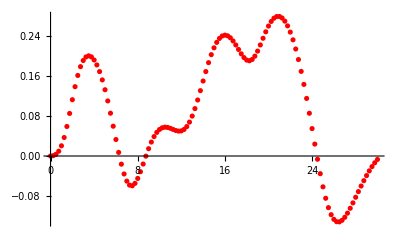

b=0.2, θA=0, θB=π/4

{{0.,{0.,0.}},{0.25,{0.000724994,0.001095}},{0.5,{0.00349404,0.00477189}},{0.75,{0.0096019,0.0117942}},{1.,{0.020472,0.0227863}},{1.25,{0.037052,0.0377639}},{1.5,{0.0591817,0.055777}},{1.75,{0.0853032,0.0749356}},{2.,{0.112817,0.092919}},{2.25,{0.138923,0.107694}},{2.5,{0.161419,0.118003}},{2.75,{0.179037,0.123415}},{3.,{0.19135,0.124093}},{3.25,{0.198465,0.120489}},{3.5,{0.200744,0.113116}},{3.75,{0.198604,0.102432}},{4.,{0.192424,0.0887952}},{4.25,{0.182512,0.0724775}},{4.5,{0.169115,0.0536915}},{4.75,{0.152451,0.0326381}},{5.,{0.132765,0.00955896}},{5.25,{0.110381,-0.0152019}},{5.5,{0.0857835,-0.0411338}},{5.75,{0.0596796,-0.0674982}},{6.,{0.0330605,-0.0932878}},{6.25,{0.0072133,-0.11723}},{6.5,{-0.0163375,-0.137867}},{6.75,{-0.0359875,-0.153721}},{7.,{-0.0502992,-0.163542}},{7.25,{-0.0582871,-0.166572}},{7.5,{-0.0596449,-0.162738}},{7.75,{-0.0548244,-0.152685}},{8.,{-0.0449313,-0.137638}},{8.25,{-0.0314805,-0.119144}},{8.5,{-0.0161059,-0.0987855}},{8.75,{-0.000316924,-0.0779606}},{9.,{0.014657,-0.0577508}},{9.25,{0.0279225,-0.038894}},{9.5,{0.0389139,-0.0218092}},{9.75,{0.0473508,-0.00665851}},{10.,{0.0531862,0.00658989}},{10.25,{0.05656,0.0181036}},{10.5,{0.0577659,0.0281406}},{10.75,{0.0572288,0.0370111}},{11.,{0.0554889,0.0450514}},{11.25,{0.053189,0.0525941}},{11.5,{0.0510521,0.0599425}},{11.75,{0.0498466,0.0673408}},{12.,{0.050335,0.0749422}},{12.25,{0.0532004,0.0827789}},{12.5,{0.0589647,0.0907415}},{12.75,{0.0679115,0.0985709}},{13.,{0.0800289,0.105876}},{13.25,{0.0950019,0.112163}},{13.5,{0.112238,0.11689}},{13.75,{0.130946,0.119515}},{14.,{0.150234,0.119543}},{14.25,{0.169209,0.116559}},{14.5,{0.187054,0.110233}},{14.75,{0.203079,0.100319}},{15.,{0.216747,0.0866447}},{15.25,{0.227672,0.0690971}},{15.5,{0.235607,0.0476185}},{15.75,{0.240437,0.0222151}},{16.,{0.24216,-0.00701669}},{16.25,{0.240894,-0.0398397}},{16.5,{0.236892,-0.0758026}},{16.75,{0.230564,-0.114142}},{17.,{0.222514,-0.153678}},{17.25,{0.21356,-0.19272}},{17.5,{0.204739,-0.229059}},{17.75,{0.197235,-0.260073}},{18.,{0.192251,-0.283032}},{18.25,{0.190784,-0.295591}},{18.5,{0.193404,-0.296327}},{18.75,{0.200084,-0.285167}},{19.,{0.210175,-0.263463}},{19.25,{0.222559,-0.233693}},{19.5,{0.235891,-0.198901}},{19.75,{0.248867,-0.162095}},{20.,{0.260386,-0.125819}},{20.25,{0.26964,-0.0919604}},{20.5,{0.276099,-0.0617296}},{20.75,{0.279464,-0.035778}},{21.,{0.279613,-0.0143274}},{21.25,{0.276528,0.00267197}},{21.5,{0.270228,0.0154405}},{21.75,{0.260784,0.0242943}},{22.,{0.248275,0.0295948}},{22.25,{0.232785,0.0317209}},{22.5,{0.214414,0.0310593}},{22.75,{0.193283,0.0280048}},{23.,{0.16956,0.0229684}},{23.25,{0.143474,0.0163875}},{23.5,{0.115352,0.00873291}},{23.75,{0.0856352,0.000521498}},{24.,{0.0549074,-0.00768928}},{24.25,{0.0238991,-0.0153092}},{24.5,{-0.00652307,-0.0217462}},{24.75,{-0.0354032,-0.0264369}},{25.,{-0.0617577,-0.0289174}},{25.25,{-0.0846815,-0.0288578}},{25.5,{-0.103439,-0.0261187}},{25.75,{-0.117559,-0.0207685}},{26.,{-0.126883,-0.0130701}},{26.25,{-0.131561,-0.00344616}},{26.5,{-0.132029,0.00758729}},{26.75,{-0.128874,0.0194714}},{27.,{-0.122803,0.0316787}},{27.25,{-0.114528,0.0437403}},{27.5,{-0.104715,0.0552685}},{27.75,{-0.0939387,0.0659587}},{28.,{-0.0826786,0.07558}},{28.25,{-0.0713166,0.0839576}},{28.5,{-0.0601457,0.0909605}},{28.75,{-0.0493953,0.0964767}},{29.,{-0.039236,0.100408}},{29.25,{-0.0298037,0.102657}},{29.5,{-0.0212144,0.103134}},{29.75,{-0.0135451,0.101709}},{30.,{-0.00687884,0.098295}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53224647 near {ϕ$53224647} = {6.102911005411260803033002275697072036564350128173828125}. NIntegrate obtained -4.05683×10^-7 and 1.93371×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$54641994 near {ϕ$54641994} = {0.198042}. NIntegrate obtained -2.08734×10^-6 and 4.38427×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55622238 near {ϕ$55622238} = {2.71198}. NIntegrate obtained 4.4353×10^-6 and 4.89799×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

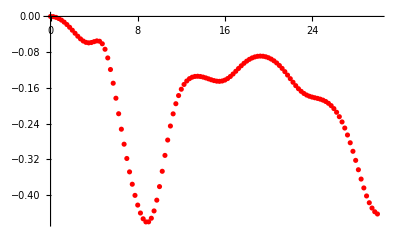

b=0.2, θA=π/4, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.000505522,-0.00170698}},{0.5,{-0.00203095,-0.00688364}},{0.75,{-0.00458336,-0.0156617}},{1.,{-0.00814898,-0.0282225}},{1.25,{-0.0126806,-0.0447879}},{1.5,{-0.018085,-0.06561}},{1.75,{-0.0242099,-0.0909524}},{2.,{-0.0308315,-0.121056}},{2.25,{-0.037643,-0.156079}},{2.5,{-0.0442513,-0.19599}},{2.75,{-0.0501852,-0.240409}},{3.,{-0.0549315,-0.288357}},{3.25,{-0.0580116,-0.33793}},{3.5,{-0.0591224,-0.385929}},{3.75,{-0.0583431,-0.427608}},{4.,{-0.056377,-0.456814}},{4.25,{-0.0547121,-0.46692}},{4.5,{-0.0555205,-0.452693}},{4.75,{-0.0611633,-0.412568}},{5.,{-0.0734238,-0.350043}},{5.25,{-0.0928744,-0.273025}},{5.5,{-0.118769,-0.191333}},{5.75,{-0.149465,-0.113878}},{6.,{-0.183045,-0.0469441}},{6.25,{-0.217793,0.00606136}},{6.5,{-0.252404,0.043996}},{6.75,{-0.28599,0.0671129}},{7.,{-0.317976,0.0763594}},{7.25,{-0.347969,0.0729403}},{7.5,{-0.375635,0.0581225}},{7.75,{-0.400588,0.0332172}},{8.,{-0.422311,-0.000314902}},{8.25,{-0.440093,-0.0406774}},{8.5,{-0.453007,-0.0855115}},{8.75,{-0.459963,-0.1317}},{9.,{-0.459844,-0.175301}},{9.25,{-0.451764,-0.211763}},{9.5,{-0.435397,-0.2365}},{9.75,{-0.411281,-0.245813}},{10.,{-0.380929,-0.237853}},{10.25,{-0.346647,-0.213219}},{10.5,{-0.311083,-0.174834}},{10.75,{-0.276688,-0.127167}},{11.,{-0.245317,-0.0751376}},{11.25,{-0.218071,-0.0232093}},{11.5,{-0.195366,0.0251527}},{11.75,{-0.17711,0.0675927}},{12.,{-0.162907,0.102723}},{12.25,{-0.152228,0.129876}},{12.5,{-0.144515,0.148854}},{12.75,{-0.139248,0.159733}},{13.,{-0.135968,0.162727}},{13.25,{-0.134288,0.158107}},{13.5,{-0.133879,0.14618}},{13.75,{-0.134461,0.1273}},{14.,{-0.135783,0.101914}},{14.25,{-0.137609,0.0706505}},{14.5,{-0.1397,0.0344297}},{14.75,{-0.141797,-0.00541038}},{15.,{-0.14362,-0.0469966}},{15.25,{-0.144869,-0.0878661}},{15.5,{-0.145246,-0.125036}},{15.75,{-0.144489,-0.155265}},{16.,{-0.142427,-0.175516}},{16.25,{-0.139028,-0.183546}},{16.5,{-0.134417,-0.178427}},{16.75,{-0.12887,-0.160817}},{17.,{-0.122763,-0.132805}},{17.25,{-0.116497,-0.0974487}},{17.5,{-0.110442,-0.0581494}},{17.75,{-0.104887,-0.0181094}},{18.,{-0.100033,0.0200151}},{18.25,{-0.0960011,0.0542402}},{18.5,{-0.0928466,0.0832238}},{18.75,{-0.0905863,0.106149}},{19.,{-0.0892151,0.122586}},{19.25,{-0.088721,0.132366}},{19.5,{-0.0890947,0.135494}},{19.75,{-0.0903341,0.132085}},{20.,{-0.0924448,0.122343}},{20.25,{-0.0954381,0.106574}},{20.5,{-0.0993269,0.085217}},{20.75,{-0.104116,0.0589058}},{21.,{-0.10979,0.0285507}},{21.25,{-0.116291,-0.00458083}},{21.5,{-0.123512,-0.038803}},{21.75,{-0.131271,-0.0720095}},{22.,{-0.139311,-0.101771}},{22.25,{-0.147311,-0.125562}},{22.5,{-0.154914,-0.141115}},{22.75,{-0.161778,-0.146823}},{23.,{-0.167642,-0.142082}},{23.25,{-0.172368,-0.127433}},{23.5,{-0.17597,-0.104459}},{23.75,{-0.178598,-0.0754601}},{24.,{-0.180509,-0.0430386}},{24.25,{-0.182018,-0.00971423}},{24.5,{-0.183457,0.0223346}},{24.75,{-0.185143,0.0513935}},{25.,{-0.187365,0.0762198}},{25.25,{-0.190377,0.0959821}},{25.5,{-0.194406,0.110172}},{25.75,{-0.19965,0.118521}},{26.,{-0.206291,0.120929}},{26.25,{-0.214494,0.117424}},{26.5,{-0.224407,0.108145}},{26.75,{-0.236151,0.0933475}},{27.,{-0.249806,0.0734418}},{27.25,{-0.265389,0.0490477}},{27.5,{-0.282822,0.0210515}},{27.75,{-0.301889,-0.00931539}},{28.,{-0.322205,-0.040441}},{28.25,{-0.343189,-0.0703422}},{28.5,{-0.364072,-0.0967802}},{28.75,{-0.383949,-0.11748}},{29.,{-0.401888,-0.130454}},{29.25,{-0.417067,-0.134351}},{29.5,{-0.428923,-0.128744}},{29.75,{-0.437257,-0.114225}},{30.,{-0.442257,-0.0922971}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$60525601 near {ϕ$60525601} = {0.503048}. NIntegrate obtained -4.4629×10^-6 and 4.66673×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$61172637 near {ϕ$61172637} = {5.12953}. NIntegrate obtained 1.11827×10^-6 and 3.00611×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$61824458 near {ϕ$61824458} = {3.36239}. NIntegrate obtained 8.27549×10^-6 and 8.32851×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

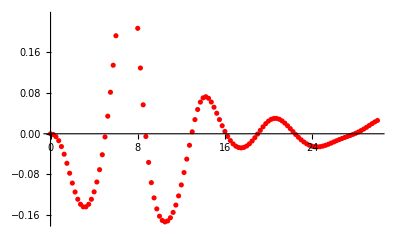

b=0.2, θA=π/2, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.00138754,0.00111195}},{0.5,{-0.00578743,0.00483611}},{0.75,{-0.0136121,0.0119627}},{1.,{-0.0251178,0.0232924}},{1.25,{-0.040165,0.0393329}},{1.5,{-0.0580543,0.0600221}},{1.75,{-0.0775139,0.0845725}},{2.,{-0.0968808,0.111531}},{2.25,{-0.114421,0.139055}},{2.5,{-0.128654,0.165299}},{2.75,{-0.138556,0.188731}},{3.,{-0.14358,0.208296}},{3.25,{-0.143562,0.223408}},{3.5,{-0.138561,0.233836}},{3.75,{-0.128711,0.239569}},{4.,{-0.114113,0.240686}},{4.25,{-0.0947679,0.237262}},{4.5,{-0.0705402,0.229324}},{4.75,{-0.0411601,0.21682}},{5.,{-0.0062526,0.199631}},{5.25,{0.034582,0.177628}},{5.5,{0.0816064,0.15077}},{5.75,{0.134649,0.119322}},{6.,{0.192606,0.0841841}},{6.25,{0.252718,0.0473775}},{6.5,{0.309771,0.0125573}},{6.75,{0.355764,-0.0148096}},{7.,{0.381011,-0.0282598}},{7.25,{0.377396,-0.0225642}},{7.5,{0.342613,0.00344759}},{7.75,{0.282203,0.0456581}},{8.,{0.207198,0.0963985}},{8.25,{0.129233,0.147787}},{8.5,{0.0568543,0.194165}},{8.75,{-0.00542735,0.232638}},{9.,{-0.056242,0.262418}},{9.25,{-0.0960322,0.283895}},{9.5,{-0.126017,0.29795}},{9.75,{-0.147582,0.305532}},{10.,{-0.161985,0.307498}},{10.25,{-0.170252,0.304536}},{10.5,{-0.173161,0.297174}},{10.75,{-0.171272,0.285813}},{11.,{-0.164969,0.270768}},{11.25,{-0.154518,0.252329}},{11.5,{-0.140124,0.230822}},{11.75,{-0.122012,0.206684}},{12.,{-0.100515,0.180543}},{12.25,{-0.0761705,0.153295}},{12.5,{-0.0498135,0.126147}},{12.75,{-0.0226391,0.100598}},{13.,{0.0038225,0.0783252}},{13.25,{0.0278389,0.0609442}},{13.5,{0.0477311,0.0496998}},{13.75,{0.0621856,0.04517}},{14.,{0.0705172,0.0471079}},{14.25,{0.0727789,0.0544974}},{14.5,{0.0696798,0.0657937}},{14.75,{0.0623634,0.0792523}},{15.,{0.0521451,0.093227}},{15.25,{0.0402922,0.106357}},{15.5,{0.0278922,0.117641}},{15.75,{0.0157963,0.126427}},{16.,{0.00462605,0.132354}},{16.25,{-0.00519216,0.135285}},{16.5,{-0.0133836,0.135247}},{16.75,{-0.0197859,0.132384}},{17.,{-0.0243185,0.126932}},{17.25,{-0.0269577,0.119205}},{17.5,{-0.0277274,0.109593}},{17.75,{-0.0266954,0.0985715}},{18.,{-0.0239758,0.0867047}},{18.25,{-0.0197376,0.0746528}},{18.5,{-0.014212,0.0631646}},{18.75,{-0.00770282,0.0530547}},{19.,{-0.00058454,0.0451598}},{19.25,{0.00670599,0.0402679}},{19.5,{0.0136941,0.0390312}},{19.75,{0.0199062,0.0418741}},{20.,{0.024916,0.0489148}},{20.25,{0.0283937,0.0599256}},{20.5,{0.0301424,0.0743457}},{20.75,{0.0301156,0.0913456}},{21.,{0.0284105,0.10993}},{21.25,{0.0252432,0.129058}},{21.5,{0.0209085,0.147744}},{21.75,{0.0157403,0.165143}},{22.,{0.0100749,0.180589}},{22.25,{0.00422632,0.193614}},{22.5,{-0.00153153,0.203937}},{22.75,{-0.00696935,0.211447}},{23.,{-0.0119038,0.216186}},{23.25,{-0.0161958,0.218322}},{23.5,{-0.0197469,0.218147}},{23.75,{-0.0224932,0.216065}},{24.,{-0.024404,0.212588}},{24.25,{-0.0254806,0.208332}},{24.5,{-0.0257555,0.20401}},{24.75,{-0.0252937,0.200402}},{25.,{-0.0241896,0.198315}},{25.25,{-0.0225645,0.198519}},{25.5,{-0.0205595,0.201664}},{25.75,{-0.0183191,0.208199}},{26.,{-0.0159815,0.218299}},{26.25,{-0.0136559,0.231826}},{26.5,{-0.0114207,0.248344}},{26.75,{-0.00930267,0.267169}},{27.,{-0.00728944,0.287465}},{27.25,{-0.00533064,0.308347}},{27.5,{-0.0033523,0.328974}},{27.75,{-0.0012715,0.348612}},{28.,{0.000993197,0.366681}},{28.25,{0.00350495,0.382753}},{28.5,{0.00630316,0.396553}},{28.75,{0.00939356,0.407939}},{29.,{0.0127415,0.416877}},{29.25,{0.0162621,0.423429}},{29.5,{0.0198142,0.427738}},{29.75,{0.0231922,0.430029}},{30.,{0.026119,0.430604}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67324132 near {ϕ$67324132} = {3.42375}. NIntegrate obtained 1.07338×10^-8 and 8.56615×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67387406 near {ϕ$67387406} = {3.42375}. NIntegrate obtained 1.49074×10^-9 and 1.26118×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67447974 near {ϕ$67447974} = {6.0097374608310267785071800972218625247478485107421875}. NIntegrate obtained 3.82013×10^-9 and 9.58044×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

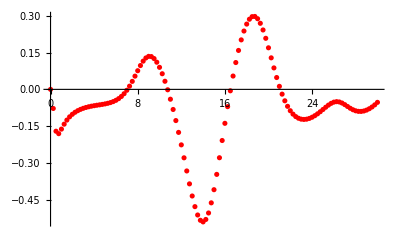

b=0.2, θA=(3 π)/4, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.0778802,-5.4789×10^-7}},{0.5,{-0.170739,3.25493×10^-7}},{0.75,{-0.180712,5.12445×10^-8}},{1.,{-0.162154,1.28004×10^-7}},{1.25,{-0.141982,1.02332×10^-7}},{1.5,{-0.125261,3.35683×10^-8}},{1.75,{-0.112059,5.88944×10^-8}},{2.,{-0.101673,1.18252×10^-7}},{2.25,{-0.0934448,2.55223×10^-8}},{2.5,{-0.086871,2.39606×10^-7}},{2.75,{-0.0815831,3.05131×10^-8}},{3.,{-0.0773036,1.07822×10^-8}},{3.25,{-0.0738209,1.56529×10^-8}},{3.5,{-0.0709648,4.84993×10^-8}},{3.75,{-0.0685899,4.84678×10^-9}},{4.,{-0.0665651,9.36338×10^-10}},{4.25,{-0.0647622,-3.96506×10^-9}},{4.5,{-0.0630501,-4.32078×10^-9}},{4.75,{-0.0612821,-8.73877×10^-9}},{5.,{-0.0592924,-1.34417×10^-8}},{5.25,{-0.0568859,-1.92352×10^-8}},{5.5,{-0.0538308,-1.2385×10^-8}},{5.75,{-0.0498511,-4.99232×10^-8}},{6.,{-0.0446232,-3.07417×10^-8}},{6.25,{-0.0377788,-2.15036×10^-8}},{6.5,{-0.0289203,-1.61541×10^-7}},{6.75,{-0.0176594,-7.68775×10^-8}},{7.,{-0.00368545,-2.6096×10^-8}},{7.25,{0.0131274,-1.17851×10^-7}},{7.5,{0.0325771,-7.04908×10^-8}},{7.75,{0.0539875,-9.7148×10^-8}},{8.,{0.0761173,-1.96554×10^-7}},{8.25,{0.0972061,-1.49126×10^-7}},{8.5,{0.115206,-8.85101×10^-8}},{8.75,{0.128165,-1.93604×10^-7}},{9.,{0.134614,-2.2921×10^-7}},{9.25,{0.133805,-1.08041×10^-8}},{9.5,{0.125711,-9.85349×10^-8}},{9.75,{0.110828,-1.55821×10^-7}},{10.,{0.089918,-4.80818×10^-8}},{10.25,{0.0637745,-1.36393×10^-7}},{10.5,{0.0330762,-8.37012×10^-8}},{10.75,{-0.00167044,5.85387×10^-8}},{11.,{-0.0401212,-7.80583×10^-8}},{11.25,{-0.082049,-1.32438×10^-8}},{11.5,{-0.127266,2.28808×10^-8}},{11.75,{-0.17553,8.31381×10^-9}},{12.,{-0.226428,-2.18508×10^-7}},{12.25,{-0.27925,1.01323×10^-6}},{12.5,{-0.332854,-1.49153×10^-7}},{12.75,{-0.38555,-1.51206×10^-7}},{13.,{-0.435035,-1.64931×10^-7}},{13.25,{-0.478436,-1.09723×10^-7}},{13.5,{-0.512532,-3.05814×10^-8}},{13.75,{-0.534148,-1.16657×10^-7}},{14.,{-0.540706,1.55321×10^-7}},{14.25,{-0.530755,4.2853×10^-7}},{14.5,{-0.504325,1.40123×10^-7}},{14.75,{-0.46295,-8.85087×10^-7}},{15.,{-0.40934,-3.57188×10^-8}},{15.25,{-0.346849,7.92525×10^-7}},{15.5,{-0.278915,2.24241×10^-7}},{15.75,{-0.20863,-1.0893×10^-7}},{16.,{-0.138514,-6.2745×10^-8}},{16.25,{-0.0704688,3.26728×10^-7}},{16.5,{-0.00585669,-1.90755×10^-7}},{16.75,{0.0543603,3.62306×10^-7}},{17.,{0.109467,5.49857×10^-7}},{17.25,{0.158857,-1.55086×10^-7}},{17.5,{0.201928,1.31904×10^-8}},{17.75,{0.238014,-1.28002×10^-7}},{18.,{0.266363,-6.8886×10^-7}},{18.25,{0.286185,-3.59989×10^-7}},{18.5,{0.296737,-1.07409×10^-7}},{18.75,{0.297496,-2.10994×10^-7}},{19.,{0.288307,-2.70821×10^-7}},{19.25,{0.269583,-4.88715×10^-7}},{19.5,{0.242358,-1.78719×10^-7}},{19.75,{0.208336,-3.35536×10^-7}},{20.,{0.169652,-1.72526×10^-7}},{20.25,{0.128649,8.50699×10^-8}},{20.5,{0.0875729,-3.24242×10^-7}},{20.75,{0.0483344,1.18822×10^-8}},{21.,{0.0123571,2.01387×10^-7}},{21.25,{-0.0194484,3.55788×10^-7}},{21.5,{-0.0466414,3.01227×10^-7}},{21.75,{-0.0691463,0.0000108993}},{22.,{-0.0871426,2.74065×10^-6}},{22.25,{-0.100963,2.66596×10^-6}},{22.5,{-0.111015,9.58497×10^-8}},{22.75,{-0.117717,-1.30247×10^-7}},{23.,{-0.121475,9.0616×10^-8}},{23.25,{-0.122652,-4.94034×10^-7}},{23.5,{-0.121569,3.62766×10^-7}},{23.75,{-0.1185,-5.05703×10^-7}},{24.,{-0.113695,-3.29376×10^-7}},{24.25,{-0.107382,-3.03677×10^-7}},{24.5,{-0.0998031,-7.9349×10^-7}},{24.75,{-0.0912516,3.21578×10^-6}},{25.,{-0.0821018,-2.24124×10^-6}},{25.25,{-0.0728672,-1.50953×10^-6}},{25.5,{-0.0642201,-1.33109×10^-6}},{25.75,{-0.0569923,-2.67228×10^-6}},{26.,{-0.0520408,-1.80041×10^-6}},{26.25,{-0.0500827,-1.41905×10^-6}},{26.5,{-0.0514242,-1.07082×10^-6}},{26.75,{-0.0557681,-3.13995×10^-7}},{27.,{-0.0622656,-2.95247×10^-7}},{27.25,{-0.0697293,2.47378×10^-7}},{27.5,{-0.0769765,-7.2795×10^-7}},{27.75,{-0.0830678,-6.88728×10^-7}},{28.,{-0.0874167,-3.52635×10^-7}},{28.25,{-0.0897388,-7.97154×10^-7}},{28.5,{-0.0899768,-5.53442×10^-7}},{28.75,{-0.0881895,-1.46167×10^-6}},{29.,{-0.084501,1.34106×10^-6}},{29.25,{-0.0790295,-1.41351×10^-6}},{29.5,{-0.0718907,-2.10026×10^-6}},{29.75,{-0.0631834,7.43283×10^-6}},{30.,{-0.0529887,-2.37755×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76175214 near {ϕ$76175214} = {1.5707}. NIntegrate obtained -3.3312×10^-7 and 3.98893×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76293410 near {ϕ$76293410} = {1.55843}. NIntegrate obtained 0.0000143233 and 1.71086×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76492245 near {ϕ$76492245} = {5.43633}. NIntegrate obtained 5.19123×10^-6 and 1.17524×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

b=0.2, θA=0, θB=-π/4

{{0.,{0.,0.}},{0.25,{0.000724994,-0.001095}},{0.5,{0.00349404,-0.00477189}},{0.75,{0.0096019,-0.0117942}},{1.,{0.020472,-0.0227863}},{1.25,{0.037052,-0.0377639}},{1.5,{0.0591817,-0.055777}},{1.75,{0.0853032,-0.0749356}},{2.,{0.112817,-0.092919}},{2.25,{0.138923,-0.107694}},{2.5,{0.161419,-0.118003}},{2.75,{0.179037,-0.123415}},{3.,{0.19135,-0.124093}},{3.25,{0.198465,-0.120489}},{3.5,{0.200744,-0.113116}},{3.75,{0.198604,-0.102432}},{4.,{0.192424,-0.0887952}},{4.25,{0.182512,-0.0724775}},{4.5,{0.169115,-0.0536915}},{4.75,{0.152451,-0.0326381}},{5.,{0.132765,-0.00955896}},{5.25,{0.110381,0.0152019}},{5.5,{0.0857835,0.0411338}},{5.75,{0.0596796,0.0674982}},{6.,{0.0330605,0.0932878}},{6.25,{0.0072133,0.11723}},{6.5,{-0.0163375,0.137867}},{6.75,{-0.0359875,0.153721}},{7.,{-0.0502992,0.163542}},{7.25,{-0.0582871,0.166572}},{7.5,{-0.0596449,0.162738}},{7.75,{-0.0548244,0.152685}},{8.,{-0.0449313,0.137638}},{8.25,{-0.0314805,0.119144}},{8.5,{-0.0161059,0.0987855}},{8.75,{-0.000316924,0.0779606}},{9.,{0.014657,0.0577508}},{9.25,{0.0279225,0.038894}},{9.5,{0.0389139,0.0218092}},{9.75,{0.0473508,0.00665851}},{10.,{0.0531862,-0.00658989}},{10.25,{0.05656,-0.0181036}},{10.5,{0.0577659,-0.0281406}},{10.75,{0.0572288,-0.0370111}},{11.,{0.0554889,-0.0450514}},{11.25,{0.053189,-0.0525941}},{11.5,{0.0510521,-0.0599425}},{11.75,{0.0498466,-0.0673408}},{12.,{0.050335,-0.0749422}},{12.25,{0.0532004,-0.0827789}},{12.5,{0.0589647,-0.0907415}},{12.75,{0.0679115,-0.0985709}},{13.,{0.0800289,-0.105876}},{13.25,{0.0950019,-0.112163}},{13.5,{0.112238,-0.11689}},{13.75,{0.130946,-0.119515}},{14.,{0.150234,-0.119543}},{14.25,{0.169209,-0.116559}},{14.5,{0.187054,-0.110233}},{14.75,{0.203079,-0.100319}},{15.,{0.216747,-0.0866447}},{15.25,{0.227672,-0.0690971}},{15.5,{0.235607,-0.0476185}},{15.75,{0.240437,-0.0222151}},{16.,{0.24216,0.00701669}},{16.25,{0.240894,0.0398397}},{16.5,{0.236892,0.0758026}},{16.75,{0.230564,0.114142}},{17.,{0.222514,0.153678}},{17.25,{0.21356,0.19272}},{17.5,{0.204739,0.229059}},{17.75,{0.197235,0.260073}},{18.,{0.192251,0.283032}},{18.25,{0.190784,0.295591}},{18.5,{0.193404,0.296327}},{18.75,{0.200084,0.285167}},{19.,{0.210175,0.263463}},{19.25,{0.222559,0.233693}},{19.5,{0.235891,0.198901}},{19.75,{0.248867,0.162095}},{20.,{0.260386,0.125819}},{20.25,{0.26964,0.0919604}},{20.5,{0.276099,0.0617296}},{20.75,{0.279464,0.035778}},{21.,{0.279613,0.0143274}},{21.25,{0.276528,-0.00267197}},{21.5,{0.270228,-0.0154405}},{21.75,{0.260784,-0.0242943}},{22.,{0.248275,-0.0295948}},{22.25,{0.232785,-0.0317209}},{22.5,{0.214414,-0.0310593}},{22.75,{0.193283,-0.0280048}},{23.,{0.16956,-0.0229684}},{23.25,{0.143474,-0.0163875}},{23.5,{0.115352,-0.00873291}},{23.75,{0.0856352,-0.000521498}},{24.,{0.0549074,0.00768928}},{24.25,{0.0238991,0.0153092}},{24.5,{-0.00652307,0.0217462}},{24.75,{-0.0354032,0.0264369}},{25.,{-0.0617577,0.0289174}},{25.25,{-0.0846815,0.0288578}},{25.5,{-0.103439,0.0261187}},{25.75,{-0.117559,0.0207685}},{26.,{-0.126883,0.0130701}},{26.25,{-0.131561,0.00344616}},{26.5,{-0.132029,-0.00758729}},{26.75,{-0.128874,-0.0194714}},{27.,{-0.122803,-0.0316787}},{27.25,{-0.114528,-0.0437403}},{27.5,{-0.104715,-0.0552685}},{27.75,{-0.0939387,-0.0659587}},{28.,{-0.0826786,-0.07558}},{28.25,{-0.0713166,-0.0839576}},{28.5,{-0.0601457,-0.0909605}},{28.75,{-0.0493953,-0.0964767}},{29.,{-0.039236,-0.100408}},{29.25,{-0.0298037,-0.102657}},{29.5,{-0.0212144,-0.103134}},{29.75,{-0.0135451,-0.101709}},{30.,{-0.00687884,-0.098295}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82441119 near {ϕ$82441119} = {2.87151}. NIntegrate obtained -1.07338×10^-8 and 8.56615×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82504393 near {ϕ$82504393} = {3.42375}. NIntegrate obtained -1.49075×10^-9 and 1.2519×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82564961 near {ϕ$82564961} = {6.0097374608310267785071800972218625247478485107421875}. NIntegrate obtained -3.82011×10^-9 and 9.73505×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

b=0.2, θA=π/4, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.0778802,5.4789×10^-7}},{0.5,{-0.170739,-3.25493×10^-7}},{0.75,{-0.180712,-5.12446×10^-8}},{1.,{-0.162154,-1.28003×10^-7}},{1.25,{-0.141982,-1.02332×10^-7}},{1.5,{-0.125261,-3.35683×10^-8}},{1.75,{-0.112059,-5.88942×10^-8}},{2.,{-0.101673,-1.18251×10^-7}},{2.25,{-0.0934448,-2.55223×10^-8}},{2.5,{-0.086871,-2.39606×10^-7}},{2.75,{-0.0815831,-3.05131×10^-8}},{3.,{-0.0773036,-1.07712×10^-8}},{3.25,{-0.0738209,-1.56529×10^-8}},{3.5,{-0.0709648,-4.84993×10^-8}},{3.75,{-0.0685899,-4.85671×10^-9}},{4.,{-0.0665651,-9.36338×10^-10}},{4.25,{-0.0647622,3.96506×10^-9}},{4.5,{-0.0630501,4.32078×10^-9}},{4.75,{-0.0612821,8.7259×10^-9}},{5.,{-0.0592924,1.34313×10^-8}},{5.25,{-0.0568859,1.92352×10^-8}},{5.5,{-0.0538308,9.64132×10^-9}},{5.75,{-0.0498511,4.99232×10^-8}},{6.,{-0.0446232,3.07417×10^-8}},{6.25,{-0.0377788,2.14084×10^-8}},{6.5,{-0.0289203,1.61541×10^-7}},{6.75,{-0.0176594,7.68775×10^-8}},{7.,{-0.00368545,2.6096×10^-8}},{7.25,{0.0131274,1.17851×10^-7}},{7.5,{0.0325771,7.239×10^-8}},{7.75,{0.0539875,9.7148×10^-8}},{8.,{0.0761173,1.96554×10^-7}},{8.25,{0.0972061,1.49126×10^-7}},{8.5,{0.115206,8.95408×10^-8}},{8.75,{0.128165,1.93604×10^-7}},{9.,{0.134614,2.41518×10^-7}},{9.25,{0.133805,6.45016×10^-9}},{9.5,{0.125711,9.88986×10^-8}},{9.75,{0.110828,1.55608×10^-7}},{10.,{0.089918,4.80818×10^-8}},{10.25,{0.0637745,1.36393×10^-7}},{10.5,{0.0330762,8.36402×10^-8}},{10.75,{-0.00167044,-5.81151×10^-8}},{11.,{-0.0401212,7.80583×10^-8}},{11.25,{-0.082049,1.3542×10^-8}},{11.5,{-0.127266,-2.28514×10^-8}},{11.75,{-0.17553,-8.31381×10^-9}},{12.,{-0.226428,2.07665×10^-7}},{12.25,{-0.27925,-1.01323×10^-6}},{12.5,{-0.332854,1.49153×10^-7}},{12.75,{-0.38555,1.51206×10^-7}},{13.,{-0.435035,1.64931×10^-7}},{13.25,{-0.478436,1.13165×10^-7}},{13.5,{-0.512532,3.02515×10^-8}},{13.75,{-0.534148,1.16657×10^-7}},{14.,{-0.540706,-1.55321×10^-7}},{14.25,{-0.530755,-4.25364×10^-7}},{14.5,{-0.504325,-1.39902×10^-7}},{14.75,{-0.46295,8.84347×10^-7}},{15.,{-0.40934,3.5775×10^-8}},{15.25,{-0.346849,-7.91846×10^-7}},{15.5,{-0.278915,-2.24241×10^-7}},{15.75,{-0.20863,1.10793×10^-7}},{16.,{-0.138514,6.4239×10^-8}},{16.25,{-0.0704688,-3.28145×10^-7}},{16.5,{-0.00585669,1.90755×10^-7}},{16.75,{0.0543603,-3.59356×10^-7}},{17.,{0.109467,-5.5033×10^-7}},{17.25,{0.158857,1.55086×10^-7}},{17.5,{0.201928,-1.98751×10^-8}},{17.75,{0.238014,1.27565×10^-7}},{18.,{0.266363,6.95046×10^-7}},{18.25,{0.286185,3.59989×10^-7}},{18.5,{0.296737,1.07409×10^-7}},{18.75,{0.297496,2.10994×10^-7}},{19.,{0.288307,2.77629×10^-7}},{19.25,{0.269583,4.88708×10^-7}},{19.5,{0.242358,1.78719×10^-7}},{19.75,{0.208336,3.39399×10^-7}},{20.,{0.169652,1.71079×10^-7}},{20.25,{0.128649,-8.50699×10^-8}},{20.5,{0.0875729,3.24242×10^-7}},{20.75,{0.0483344,5.77031×10^-8}},{21.,{0.0123571,-2.00388×10^-7}},{21.25,{-0.0194484,-3.55788×10^-7}},{21.5,{-0.0466414,-3.01227×10^-7}},{21.75,{-0.0691463,-0.0000108993}},{22.,{-0.0871426,-2.74065×10^-6}},{22.25,{-0.100963,-2.66596×10^-6}},{22.5,{-0.111015,-9.58497×10^-8}},{22.75,{-0.117717,1.30247×10^-7}},{23.,{-0.121475,-9.0616×10^-8}},{23.25,{-0.122652,4.42931×10^-7}},{23.5,{-0.121569,-3.62766×10^-7}},{23.75,{-0.1185,4.73286×10^-7}},{24.,{-0.113695,2.68072×10^-7}},{24.25,{-0.107382,2.88428×10^-7}},{24.5,{-0.0998031,7.9349×10^-7}},{24.75,{-0.0912516,-3.21578×10^-6}},{25.,{-0.0821018,2.24124×10^-6}},{25.25,{-0.0728672,1.50953×10^-6}},{25.5,{-0.0642201,1.19022×10^-6}},{25.75,{-0.0569923,2.67228×10^-6}},{26.,{-0.0520408,1.80041×10^-6}},{26.25,{-0.0500827,1.37217×10^-6}},{26.5,{-0.0514242,1.07082×10^-6}},{26.75,{-0.0557681,3.93934×10^-7}},{27.,{-0.0622656,2.38157×10^-7}},{27.25,{-0.0697293,-2.47378×10^-7}},{27.5,{-0.0769765,7.9245×10^-7}},{27.75,{-0.0830678,6.69831×10^-7}},{28.,{-0.0874167,2.64232×10^-7}},{28.25,{-0.0897388,7.97154×10^-7}},{28.5,{-0.0899768,5.53442×10^-7}},{28.75,{-0.0881895,1.37978×10^-6}},{29.,{-0.084501,-1.34106×10^-6}},{29.25,{-0.0790295,1.41351×10^-6}},{29.5,{-0.0718907,2.12939×10^-6}},{29.75,{-0.0631834,-7.43283×10^-6}},{30.,{-0.0529887,2.37755×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$91164564 near {ϕ$91164564} = {5.79221}. NIntegrate obtained -4.4629×10^-6 and 4.66673×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$91811720 near {ϕ$91811720} = {1.16573}. NIntegrate obtained 1.11827×10^-6 and 3.00611×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$92462317 near {ϕ$92462317} = {2.93287}. NIntegrate obtained 8.27549×10^-6 and 8.32851×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

b=0.2, θA=π/2, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.00138754,-0.00111195}},{0.5,{-0.00578743,-0.00483611}},{0.75,{-0.0136121,-0.0119627}},{1.,{-0.0251178,-0.0232924}},{1.25,{-0.040165,-0.0393329}},{1.5,{-0.0580543,-0.0600221}},{1.75,{-0.0775139,-0.0845725}},{2.,{-0.0968808,-0.111531}},{2.25,{-0.114421,-0.139055}},{2.5,{-0.128654,-0.165299}},{2.75,{-0.138556,-0.188731}},{3.,{-0.14358,-0.208296}},{3.25,{-0.143562,-0.223408}},{3.5,{-0.138561,-0.233836}},{3.75,{-0.128711,-0.239569}},{4.,{-0.114113,-0.240686}},{4.25,{-0.0947679,-0.237262}},{4.5,{-0.0705402,-0.229324}},{4.75,{-0.0411601,-0.21682}},{5.,{-0.0062526,-0.199631}},{5.25,{0.034582,-0.177628}},{5.5,{0.0816064,-0.15077}},{5.75,{0.134649,-0.119322}},{6.,{0.192606,-0.0841841}},{6.25,{0.252718,-0.0473775}},{6.5,{0.309771,-0.0125573}},{6.75,{0.355764,0.0148096}},{7.,{0.381011,0.0282598}},{7.25,{0.377396,0.0225642}},{7.5,{0.342613,-0.00344759}},{7.75,{0.282203,-0.0456581}},{8.,{0.207198,-0.0963985}},{8.25,{0.129233,-0.147787}},{8.5,{0.0568543,-0.194165}},{8.75,{-0.00542735,-0.232638}},{9.,{-0.056242,-0.262418}},{9.25,{-0.0960322,-0.283895}},{9.5,{-0.126017,-0.29795}},{9.75,{-0.147582,-0.305532}},{10.,{-0.161985,-0.307498}},{10.25,{-0.170252,-0.304536}},{10.5,{-0.173161,-0.297174}},{10.75,{-0.171272,-0.285813}},{11.,{-0.164969,-0.270768}},{11.25,{-0.154518,-0.252329}},{11.5,{-0.140124,-0.230822}},{11.75,{-0.122012,-0.206684}},{12.,{-0.100515,-0.180543}},{12.25,{-0.0761705,-0.153295}},{12.5,{-0.0498135,-0.126147}},{12.75,{-0.0226391,-0.100598}},{13.,{0.0038225,-0.0783252}},{13.25,{0.0278389,-0.0609442}},{13.5,{0.0477311,-0.0496998}},{13.75,{0.0621856,-0.04517}},{14.,{0.0705172,-0.0471079}},{14.25,{0.0727789,-0.0544974}},{14.5,{0.0696798,-0.0657937}},{14.75,{0.0623634,-0.0792523}},{15.,{0.0521451,-0.093227}},{15.25,{0.0402922,-0.106357}},{15.5,{0.0278922,-0.117641}},{15.75,{0.0157963,-0.126427}},{16.,{0.00462605,-0.132354}},{16.25,{-0.00519216,-0.135285}},{16.5,{-0.0133836,-0.135247}},{16.75,{-0.0197859,-0.132384}},{17.,{-0.0243185,-0.126932}},{17.25,{-0.0269577,-0.119205}},{17.5,{-0.0277274,-0.109593}},{17.75,{-0.0266954,-0.0985715}},{18.,{-0.0239758,-0.0867047}},{18.25,{-0.0197376,-0.0746528}},{18.5,{-0.014212,-0.0631646}},{18.75,{-0.00770282,-0.0530547}},{19.,{-0.00058454,-0.0451598}},{19.25,{0.00670599,-0.0402679}},{19.5,{0.0136941,-0.0390312}},{19.75,{0.0199062,-0.0418741}},{20.,{0.024916,-0.0489148}},{20.25,{0.0283937,-0.0599256}},{20.5,{0.0301424,-0.0743457}},{20.75,{0.0301156,-0.0913456}},{21.,{0.0284105,-0.10993}},{21.25,{0.0252432,-0.129058}},{21.5,{0.0209085,-0.147744}},{21.75,{0.0157403,-0.165143}},{22.,{0.0100749,-0.180589}},{22.25,{0.00422632,-0.193614}},{22.5,{-0.00153153,-0.203937}},{22.75,{-0.00696935,-0.211447}},{23.,{-0.0119038,-0.216186}},{23.25,{-0.0161958,-0.218322}},{23.5,{-0.0197469,-0.218147}},{23.75,{-0.0224932,-0.216065}},{24.,{-0.024404,-0.212588}},{24.25,{-0.0254806,-0.208332}},{24.5,{-0.0257555,-0.20401}},{24.75,{-0.0252937,-0.200402}},{25.,{-0.0241896,-0.198315}},{25.25,{-0.0225645,-0.198519}},{25.5,{-0.0205595,-0.201664}},{25.75,{-0.0183191,-0.208199}},{26.,{-0.0159815,-0.218299}},{26.25,{-0.0136559,-0.231826}},{26.5,{-0.0114207,-0.248344}},{26.75,{-0.00930267,-0.267169}},{27.,{-0.00728944,-0.287465}},{27.25,{-0.00533064,-0.308347}},{27.5,{-0.0033523,-0.328974}},{27.75,{-0.0012715,-0.348612}},{28.,{0.000993197,-0.366681}},{28.25,{0.00350495,-0.382753}},{28.5,{0.00630316,-0.396553}},{28.75,{0.00939356,-0.407939}},{29.,{0.0127415,-0.416877}},{29.25,{0.0162621,-0.423429}},{29.5,{0.0198142,-0.427738}},{29.75,{0.0231922,-0.430029}},{30.,{0.026119,-0.430604}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$98507832 near {ϕ$98507832} = {0.180274}. NIntegrate obtained 4.05683×10^-7 and 1.93371×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$99927026 near {ϕ$99927026} = {6.08514306664643045419182953992276452481746673583984375}. NIntegrate obtained 2.08734×10^-6 and 4.38427×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$100908553 near {ϕ$100908553} = {3.58328}. NIntegrate obtained -4.4353×10^-6 and 4.89799×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

b=0.2, θA=(3 π)/4, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.000505522,0.00170698}},{0.5,{-0.00203095,0.00688364}},{0.75,{-0.00458336,0.0156617}},{1.,{-0.00814898,0.0282225}},{1.25,{-0.0126806,0.0447879}},{1.5,{-0.018085,0.06561}},{1.75,{-0.0242099,0.0909524}},{2.,{-0.0308315,0.121056}},{2.25,{-0.037643,0.156079}},{2.5,{-0.0442513,0.19599}},{2.75,{-0.0501852,0.240409}},{3.,{-0.0549315,0.288357}},{3.25,{-0.0580116,0.33793}},{3.5,{-0.0591224,0.385929}},{3.75,{-0.0583431,0.427608}},{4.,{-0.056377,0.456814}},{4.25,{-0.0547121,0.46692}},{4.5,{-0.0555205,0.452693}},{4.75,{-0.0611633,0.412568}},{5.,{-0.0734238,0.350043}},{5.25,{-0.0928744,0.273025}},{5.5,{-0.118769,0.191333}},{5.75,{-0.149465,0.113878}},{6.,{-0.183045,0.0469441}},{6.25,{-0.217793,-0.00606136}},{6.5,{-0.252404,-0.043996}},{6.75,{-0.28599,-0.0671129}},{7.,{-0.317976,-0.0763594}},{7.25,{-0.347969,-0.0729403}},{7.5,{-0.375635,-0.0581225}},{7.75,{-0.400588,-0.0332172}},{8.,{-0.422311,0.000314902}},{8.25,{-0.440093,0.0406774}},{8.5,{-0.453007,0.0855115}},{8.75,{-0.459963,0.1317}},{9.,{-0.459844,0.175301}},{9.25,{-0.451764,0.211763}},{9.5,{-0.435397,0.2365}},{9.75,{-0.411281,0.245813}},{10.,{-0.380929,0.237853}},{10.25,{-0.346647,0.213219}},{10.5,{-0.311083,0.174834}},{10.75,{-0.276688,0.127167}},{11.,{-0.245317,0.0751376}},{11.25,{-0.218071,0.0232093}},{11.5,{-0.195366,-0.0251527}},{11.75,{-0.17711,-0.0675927}},{12.,{-0.162907,-0.102723}},{12.25,{-0.152228,-0.129876}},{12.5,{-0.144515,-0.148854}},{12.75,{-0.139248,-0.159733}},{13.,{-0.135968,-0.162727}},{13.25,{-0.134288,-0.158107}},{13.5,{-0.133879,-0.14618}},{13.75,{-0.134461,-0.1273}},{14.,{-0.135783,-0.101914}},{14.25,{-0.137609,-0.0706505}},{14.5,{-0.1397,-0.0344297}},{14.75,{-0.141797,0.00541038}},{15.,{-0.14362,0.0469966}},{15.25,{-0.144869,0.0878661}},{15.5,{-0.145246,0.125036}},{15.75,{-0.144489,0.155265}},{16.,{-0.142427,0.175516}},{16.25,{-0.139028,0.183546}},{16.5,{-0.134417,0.178427}},{16.75,{-0.12887,0.160817}},{17.,{-0.122763,0.132805}},{17.25,{-0.116497,0.0974487}},{17.5,{-0.110442,0.0581494}},{17.75,{-0.104887,0.0181094}},{18.,{-0.100033,-0.0200151}},{18.25,{-0.0960011,-0.0542402}},{18.5,{-0.0928466,-0.0832238}},{18.75,{-0.0905863,-0.106149}},{19.,{-0.0892151,-0.122586}},{19.25,{-0.088721,-0.132366}},{19.5,{-0.0890947,-0.135494}},{19.75,{-0.0903341,-0.132085}},{20.,{-0.0924448,-0.122343}},{20.25,{-0.0954381,-0.106574}},{20.5,{-0.0993269,-0.085217}},{20.75,{-0.104116,-0.0589058}},{21.,{-0.10979,-0.0285507}},{21.25,{-0.116291,0.00458083}},{21.5,{-0.123512,0.038803}},{21.75,{-0.131271,0.0720095}},{22.,{-0.139311,0.101771}},{22.25,{-0.147311,0.125562}},{22.5,{-0.154914,0.141115}},{22.75,{-0.161778,0.146823}},{23.,{-0.167642,0.142082}},{23.25,{-0.172368,0.127433}},{23.5,{-0.17597,0.104459}},{23.75,{-0.178598,0.0754601}},{24.,{-0.180509,0.0430386}},{24.25,{-0.182018,0.00971423}},{24.5,{-0.183457,-0.0223346}},{24.75,{-0.185143,-0.0513935}},{25.,{-0.187365,-0.0762198}},{25.25,{-0.190377,-0.0959821}},{25.5,{-0.194406,-0.110172}},{25.75,{-0.19965,-0.118521}},{26.,{-0.206291,-0.120929}},{26.25,{-0.214494,-0.117424}},{26.5,{-0.224407,-0.108145}},{26.75,{-0.236151,-0.0933475}},{27.,{-0.249806,-0.0734418}},{27.25,{-0.265389,-0.0490477}},{27.5,{-0.282822,-0.0210515}},{27.75,{-0.301889,0.00931539}},{28.,{-0.322205,0.040441}},{28.25,{-0.343189,0.0703422}},{28.5,{-0.364072,0.0967802}},{28.75,{-0.383949,0.11748}},{29.,{-0.401888,0.130454}},{29.25,{-0.417067,0.134351}},{29.5,{-0.428923,0.128744}},{29.75,{-0.437257,0.114225}},{30.,{-0.442257,0.0922971}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$105344994 near {ϕ$105344994} = {2.25792}. NIntegrate obtained -1.7486×10^-15 and 4.09086×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$105396550 near {ϕ$105396550} = {2.54017}. NIntegrate obtained -2.56739×10^-16 and 9.72489×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$105438553 near {ϕ$105438553} = {3.71827}. NIntegrate obtained -2.01662×10^-16 and 5.40433×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

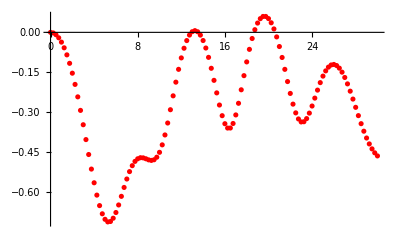

b=0.2, θA=0, θB=0

{{0.,{0.,0.}},{0.25,{-0.00223142,-7.01506×10^-17}},{0.5,{-0.00899626,-4.41098×10^-17}},{0.75,{-0.0204449,-8.54947×10^-17}},{1.,{-0.0367562,1.02218×10^-17}},{1.25,{-0.0581102,6.46433×10^-19}},{1.5,{-0.084659,-9.04168×10^-16}},{1.75,{-0.11649,-6.0564×10^-17}},{2.,{-0.153584,1.01667×10^-13}},{2.25,{-0.195761,-4.75814×10^-17}},{2.5,{-0.242627,8.98457×10^-10}},{2.75,{-0.293527,-1.46584×10^-11}},{3.,{-0.347514,4.24822×10^-14}},{3.25,{-0.403344,-4.59235×10^-17}},{3.5,{-0.459506,-9.8827×10^-17}},{3.75,{-0.514278,4.84346×10^-9}},{4.,{-0.565813,8.87356×10^-14}},{4.25,{-0.612224,-1.33253×10^-17}},{4.5,{-0.651675,-1.05456×10^-16}},{4.75,{-0.682477,-2.76509×10^-17}},{5.,{-0.703222,3.17699×10^-17}},{5.25,{-0.71296,-1.54873×10^-16}},{5.5,{-0.71141,8.72043×10^-14}},{5.75,{-0.699142,-3.64219×10^-10}},{6.,{-0.677656,-7.10007×10^-13}},{6.25,{-0.649272,4.4343×10^-9}},{6.5,{-0.616847,-1.17405×10^-8}},{6.75,{-0.58338,-3.0819×10^-12}},{7.,{-0.551627,1.31387×10^-16}},{7.25,{-0.523806,-8.40433×10^-10}},{7.5,{-0.501445,-5.7706×10^-12}},{7.75,{-0.485334,6.10922×10^-12}},{8.,{-0.475559,1.37188×10^-9}},{8.25,{-0.471546,1.21454×10^-11}},{8.5,{-0.472116,-1.8292×10^-9}},{8.75,{-0.475532,-1.06641×10^-12}},{9.,{-0.479579,8.59305×10^-18}},{9.25,{-0.481694,1.13477×10^-11}},{9.5,{-0.479202,-3.97242×10^-18}},{9.75,{-0.469658,-2.38119×10^-11}},{10.,{-0.451253,-1.90241×10^-8}},{10.25,{-0.423191,5.51182×10^-10}},{10.5,{-0.385902,-2.11128×10^-16}},{10.75,{-0.341001,-7.67709×10^-12}},{11.,{-0.290987,-7.95563×10^-9}},{11.25,{-0.238792,-4.55382×10^-16}},{11.5,{-0.187319,-7.36423×10^-16}},{11.75,{-0.1391,-1.65295×10^-10}},{12.,{-0.0961056,-4.42901×10^-16}},{12.25,{-0.0597501,-1.35243×10^-11}},{12.5,{-0.0309287,1.32809×10^-10}},{12.75,{-0.0101559,1.69111×10^-10}},{13.,{0.00232166,-1.62238×10^-10}},{13.25,{0.00642656,-1.79371×10^-10}},{13.5,{0.00218797,2.15495×10^-8}},{13.75,{-0.0102833,-1.94741×10^-10}},{14.,{-0.0307762,-2.06807×10^-10}},{14.25,{-0.0589188,-1.76045×10^-10}},{14.5,{-0.0940683,-1.50742×10^-10}},{14.75,{-0.135158,3.67017×10^-10}},{15.,{-0.180512,-1.84406×10^-8}},{15.25,{-0.227677,-3.54253×10^-11}},{15.5,{-0.273338,-3.02428×10^-9}},{15.75,{-0.313441,2.59587×10^-16}},{16.,{-0.343619,-1.59321×10^-10}},{16.25,{-0.359946,-2.65654×10^-9}},{16.5,{-0.359841,-8.25983×10^-10}},{16.75,{-0.342798,-2.81394×10^-11}},{17.,{-0.310588,-1.48962×10^-10}},{17.25,{-0.266816,-2.82065×10^-10}},{17.5,{-0.216043,-5.69126×10^-10}},{17.75,{-0.162854,-1.80516×10^-10}},{18.,{-0.111173,-1.98581×10^-10}},{18.25,{-0.0639552,1.97709×10^-10}},{18.5,{-0.0231792,3.73815×10^-10}},{18.75,{0.0099878,2.9769×10^-9}},{19.,{0.0349667,2.52096×10^-11}},{19.25,{0.0515548,1.62368×10^-11}},{19.5,{0.0597819,1.30572×10^-9}},{19.75,{0.0597859,5.16779×10^-10}},{20.,{0.0517777,6.0729×10^-10}},{20.25,{0.036026,7.06099×10^-10}},{20.5,{0.0128833,4.42549×10^-10}},{20.75,{-0.0171454,5.16062×10^-10}},{21.,{-0.0533106,1.15303×10^-9}},{21.25,{-0.0945033,1.93024×10^-10}},{21.5,{-0.139144,-2.17417×10^-16}},{21.75,{-0.185105,6.86545×10^-10}},{22.,{-0.229733,-7.4828×10^-9}},{22.25,{-0.270006,3.47888×10^-8}},{22.5,{-0.302876,3.86031×10^-10}},{22.75,{-0.325745,-2.507×10^-9}},{23.,{-0.336961,-4.27319×10^-9}},{23.25,{-0.336177,-1.40366×10^-9}},{23.5,{-0.324404,-5.01776×10^-9}},{23.75,{-0.303778,-1.12918×10^-9}},{24.,{-0.277102,1.22952×10^-9}},{24.25,{-0.247346,-3.89162×10^-10}},{24.5,{-0.217252,1.64592×10^-10}},{24.75,{-0.189093,-4.75687×10^-9}},{25.,{-0.164588,-3.27535×10^-10}},{25.25,{-0.144928,-1.22697×10^-7}},{25.5,{-0.130863,2.23927×10^-9}},{25.75,{-0.122777,1.53814×10^-9}},{26.,{-0.120792,2.23854×10^-9}},{26.25,{-0.124823,-3.66112×10^-9}},{26.5,{-0.134616,2.36875×10^-9}},{26.75,{-0.149765,2.26707×10^-9}},{27.,{-0.169732,-4.29688×10^-9}},{27.25,{-0.193831,1.87963×10^-9}},{27.5,{-0.221235,1.78883×10^-9}},{27.75,{-0.250987,5.81859×10^-9}},{28.,{-0.282025,4.0211×10^-9}},{28.25,{-0.313233,3.15082×10^-9}},{28.5,{-0.343505,2.22063×10^-9}},{28.75,{-0.371839,-3.52926×10^-8}},{29.,{-0.39741,-3.90627×10^-10}},{29.25,{-0.41964,5.35413×10^-8}},{29.5,{-0.438236,2.47172×10^-7}},{29.75,{-0.453188,2.70165×10^-8}},{30.,{-0.464744,-5.39302×10^-9}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$115066606 near {ϕ$115066606} = {3.50965}. NIntegrate obtained -3.33091×10^-7 and 4.84614×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$115640765 near {ϕ$115640765} = {1.178}. NIntegrate obtained 0.0000203501 and 2.38985×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$116491325 near {ϕ$116491325} = {4.24596}. NIntegrate obtained 7.81986×10^-6 and 8.12518×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

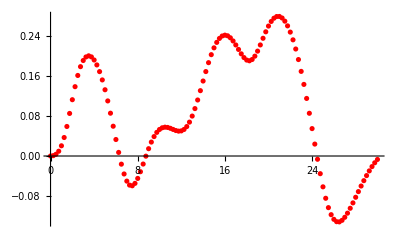

b=0.2, θA=π/4, θB=0

{{0.,{0.,0.}},{0.25,{0.000725102,0.00109495}},{0.5,{0.00349403,0.00477194}},{0.75,{0.00960184,0.0117943}},{1.,{0.020472,0.0227864}},{1.25,{0.0370519,0.0377639}},{1.5,{0.0591817,0.0557771}},{1.75,{0.0853032,0.0749357}},{2.,{0.112816,0.0929191}},{2.25,{0.138923,0.107694}},{2.5,{0.161419,0.118003}},{2.75,{0.179037,0.123415}},{3.,{0.19135,0.124093}},{3.25,{0.198465,0.120489}},{3.5,{0.200744,0.113116}},{3.75,{0.198604,0.102432}},{4.,{0.192424,0.0887953}},{4.25,{0.182512,0.0724775}},{4.5,{0.169115,0.0536915}},{4.75,{0.152451,0.0326381}},{5.,{0.132765,0.00955902}},{5.25,{0.110381,-0.0152018}},{5.5,{0.0857834,-0.0411337}},{5.75,{0.0596795,-0.0674981}},{6.,{0.0330604,-0.0932877}},{6.25,{0.00721326,-0.11723}},{6.5,{-0.0163377,-0.137867}},{6.75,{-0.0359875,-0.153721}},{7.,{-0.0502993,-0.163541}},{7.25,{-0.0582872,-0.166572}},{7.5,{-0.059645,-0.162738}},{7.75,{-0.0548245,-0.152685}},{8.,{-0.0449314,-0.137638}},{8.25,{-0.0314806,-0.119144}},{8.5,{-0.0161059,-0.0987855}},{8.75,{-0.000316896,-0.0779607}},{9.,{0.0146572,-0.057751}},{9.25,{0.0279225,-0.038894}},{9.5,{0.0389139,-0.0218093}},{9.75,{0.0473509,-0.00665869}},{10.,{0.0531862,0.00658972}},{10.25,{0.0565599,0.0181034}},{10.5,{0.0577661,0.0281403}},{10.75,{0.0572285,0.0370114}},{11.,{0.0554889,0.0450514}},{11.25,{0.0531889,0.0525941}},{11.5,{0.051052,0.0599426}},{11.75,{0.0498469,0.0673409}},{12.,{0.0503352,0.0749423}},{12.25,{0.0532004,0.0827789}},{12.5,{0.0589645,0.0907416}},{12.75,{0.0679108,0.0985708}},{13.,{0.0800289,0.105876}},{13.25,{0.0950018,0.112163}},{13.5,{0.112238,0.11689}},{13.75,{0.130946,0.119515}},{14.,{0.150234,0.119543}},{14.25,{0.16921,0.116559}},{14.5,{0.187054,0.110233}},{14.75,{0.203079,0.100319}},{15.,{0.216747,0.0866448}},{15.25,{0.227672,0.0690976}},{15.5,{0.235607,0.0476186}},{15.75,{0.240437,0.0222151}},{16.,{0.24216,-0.00701659}},{16.25,{0.240894,-0.0398395}},{16.5,{0.236892,-0.0758024}},{16.75,{0.230564,-0.114142}},{17.,{0.222513,-0.153677}},{17.25,{0.21356,-0.19272}},{17.5,{0.204739,-0.229059}},{17.75,{0.197236,-0.260072}},{18.,{0.19225,-0.283031}},{18.25,{0.190783,-0.29559}},{18.5,{0.193405,-0.296327}},{18.75,{0.200085,-0.285166}},{19.,{0.210176,-0.263461}},{19.25,{0.222559,-0.233692}},{19.5,{0.235893,-0.198901}},{19.75,{0.248868,-0.162094}},{20.,{0.260388,-0.125819}},{20.25,{0.26964,-0.0919598}},{20.5,{0.2761,-0.0617294}},{20.75,{0.279473,-0.0357722}},{21.,{0.279628,-0.0143218}},{21.25,{0.276528,0.0026723}},{21.5,{0.270228,0.0154404}},{21.75,{0.260785,0.0242952}},{22.,{0.248275,0.0295956}},{22.25,{0.232786,0.031722}},{22.5,{0.214415,0.0310603}},{22.75,{0.193285,0.0280063}},{23.,{0.169562,0.02297}},{23.25,{0.143476,0.0163893}},{23.5,{0.115353,0.00873465}},{23.75,{0.0856359,0.000522807}},{24.,{0.0549066,-0.00768745}},{24.25,{0.0238991,-0.0153074}},{24.5,{-0.00652392,-0.0217422}},{24.75,{-0.0354046,-0.0264356}},{25.,{-0.0617606,-0.0289152}},{25.25,{-0.0846838,-0.0288559}},{25.5,{-0.103443,-0.0261179}},{25.75,{-0.117563,-0.0207672}},{26.,{-0.126886,-0.0130681}},{26.25,{-0.131564,-0.00344559}},{26.5,{-0.132031,0.00758624}},{26.75,{-0.128878,0.0194712}},{27.,{-0.122807,0.0316777}},{27.25,{-0.114533,0.0437381}},{27.5,{-0.104719,0.0552668}},{27.75,{-0.0939436,0.0659565}},{28.,{-0.0826844,0.0755766}},{28.25,{-0.071323,0.0839554}},{28.5,{-0.0601539,0.0909564}},{28.75,{-0.0494038,0.09647}},{29.,{-0.0392458,0.1004}},{29.25,{-0.0298165,0.102648}},{29.5,{-0.0212264,0.103114}},{29.75,{-0.0135577,0.101701}},{30.,{-0.00689048,0.098288}}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$121311497 near {ϕ$121311497} = {4.08643}. NIntegrate obtained -1.47451×10^-17 and 1.47578×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$121360146 near {ϕ$121360146} = {4.0987}. NIntegrate obtained -8.26572×10^-14 and 1.92698×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$121411866 near {ϕ$121411866} = {4.0987}. NIntegrate obtained -3.21803×10^-14 and 3.3151×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

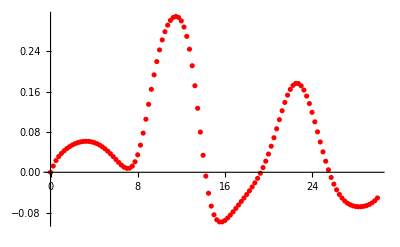

b=0.2, θA=π/2, θB=0

{{0.,{0.,0.}},{0.25,{0.0124032,-1.36277×10^-15}},{0.5,{0.0232617,-4.88644×10^-12}},{0.75,{0.0311726,-1.45428×10^-12}},{1.,{0.0374768,-5.10759×10^-13}},{1.25,{0.0427323,1.23072×10^-13}},{1.5,{0.0471897,-1.1101×10^-12}},{1.75,{0.0509732,-7.31084×10^-13}},{2.,{0.0541472,7.7999×10^-12}},{2.25,{0.0567448,9.89751×10^-12}},{2.5,{0.0587808,1.23303×10^-11}},{2.75,{0.0602582,-1.49823×10^-14}},{3.,{0.0611725,5.36361×10^-13}},{3.25,{0.0615135,4.24396×10^-12}},{3.5,{0.0612673,4.56998×10^-12}},{3.75,{0.0604177,-3.13703×10^-10}},{4.,{0.0589473,-2.27763×10^-12}},{4.25,{0.0568407,5.92351×10^-17}},{4.5,{0.0540861,-4.39962×10^-9}},{4.75,{0.0506804,-1.80723×10^-10}},{5.,{0.0466349,-9.58588×10^-11}},{5.25,{0.0419839,-8.80678×10^-13}},{5.5,{0.036797,4.17224×10^-10}},{5.75,{0.0311951,1.94246×10^-10}},{6.,{0.0253723,1.29321×10^-9}},{6.25,{0.0196224,2.92721×10^-11}},{6.5,{0.0143681,7.99258×10^-12}},{6.75,{0.0101877,1.68721×10^-10}},{7.,{0.00782736,-1.82196×10^-9}},{7.25,{0.00818232,-7.11599×10^-12}},{7.5,{0.0122223,6.80618×10^-12}},{7.75,{0.0208468,-3.78567×10^-12}},{8.,{0.0346759,1.01392×10^-10}},{8.25,{0.053827,-5.5524×10^-11}},{8.5,{0.0777663,2.27789×10^-7}},{8.75,{0.105324,-1.80304×10^-10}},{9.,{0.1349,-1.92045×10^-9}},{9.25,{0.16478,-9.05529×10^-10}},{9.5,{0.193445,1.04442×10^-9}},{9.75,{0.219759,3.91464×10^-10}},{10.,{0.243018,1.42952×10^-9}},{10.25,{0.262877,-1.80527×10^-9}},{10.5,{0.279233,2.09412×10^-10}},{10.75,{0.292096,2.25402×10^-10}},{11.,{0.301481,-5.22303×10^-10}},{11.25,{0.307323,2.35408×10^-9}},{11.5,{0.309417,5.69406×10^-10}},{11.75,{0.307377,1.37582×10^-10}},{12.,{0.300623,-2.32537×10^-10}},{12.25,{0.288408,-9.262×10^-10}},{12.5,{0.269905,-6.2418×10^-10}},{12.75,{0.244392,3.81664×10^-11}},{13.,{0.211564,-1.67688×10^-8}},{13.25,{0.171911,-1.29266×10^-9}},{13.5,{0.127057,2.23496×10^-9}},{13.75,{0.0798106,-6.80751×10^-10}},{14.,{0.0337526,2.66579×10^-10}},{14.25,{-0.00759627,1.35539×10^-9}},{14.5,{-0.0416338,-1.32445×10^-10}},{14.75,{-0.0671692,1.97558×10^-9}},{15.,{-0.0843668,3.58438×10^-9}},{15.25,{-0.0943236,-1.99316×10^-9}},{15.5,{-0.0985448,2.03764×10^-9}},{15.75,{-0.098546,3.25374×10^-9}},{16.,{-0.0956466,-2.26838×10^-10}},{16.25,{-0.0908854,2.99393×10^-11}},{16.5,{-0.0850082,-9.30273×10^-9}},{16.75,{-0.0785314,2.02919×10^-8}},{17.,{-0.0717777,4.05115×10^-10}},{17.25,{-0.0649288,1.17118×10^-10}},{17.5,{-0.0580545,-1.30445×10^-9}},{17.75,{-0.0511465,1.5996×10^-9}},{18.,{-0.04413,-2.55953×10^-9}},{18.25,{-0.0368827,1.68788×10^-8}},{18.5,{-0.0292419,1.79451×10^-8}},{18.75,{-0.0210142,3.3128×10^-9}},{19.,{-0.011986,9.53344×10^-10}},{19.25,{-0.00193813,1.45165×10^-8}},{19.5,{0.00934089,-8.502×10^-8}},{19.75,{0.0220008,7.03615×10^-10}},{20.,{0.0361469,-5.16222×10^-10}},{20.25,{0.0517454,8.27968×10^-11}},{20.5,{0.0686149,-3.01687×10^-9}},{20.75,{0.086385,-2.46744×10^-9}},{21.,{0.104498,-2.34443×10^-10}},{21.25,{0.12222,-1.28202×10^-8}},{21.5,{0.138709,1.57749×10^-9}},{21.75,{0.153092,-3.03292×10^-7}},{22.,{0.164566,1.43636×10^-8}},{22.25,{0.172481,2.30413×10^-8}},{22.5,{0.176399,6.46393×10^-8}},{22.75,{0.176119,6.61592×10^-9}},{23.,{0.171667,1.31357×10^-8}},{23.25,{0.163275,2.90149×10^-8}},{23.5,{0.151341,-2.79236×10^-9}},{23.75,{0.136406,-8.27329×10^-9}},{24.,{0.119103,1.4798×10^-9}},{24.25,{0.100142,1.87362×10^-8}},{24.5,{0.0802484,2.69181×10^-9}},{24.75,{0.0601554,-8.28332×10^-9}},{25.,{0.0405332,5.30887×10^-7}},{25.25,{0.0219631,-2.85871×10^-8}},{25.5,{0.00490676,3.25756×10^-8}},{25.75,{-0.0103197,-4.54576×10^-9}},{26.,{-0.0235434,-5.38822×10^-9}},{26.25,{-0.0347251,4.83405×10^-9}},{26.5,{-0.0439334,-3.99273×10^-7}},{26.75,{-0.0513148,1.60874×10^-10}},{27.,{-0.0570545,-5.96789×10^-9}},{27.25,{-0.0613921,-3.62716×10^-9}},{27.5,{-0.0645197,-1.31848×10^-8}},{27.75,{-0.0666355,-2.85285×10^-9}},{28.,{-0.0679015,1.48138×10^-8}},{28.25,{-0.0684361,-1.85652×10^-7}},{28.5,{-0.068312,1.1923×10^-9}},{28.75,{-0.0675503,8.35652×10^-9}},{29.,{-0.0661197,2.29105×10^-9}},{29.25,{-0.0639306,1.71552×10^-9}},{29.5,{-0.0608359,-5.7317×10^-9}},{29.75,{-0.0566231,-5.77209×10^-9}},{30.,{-0.0510263,-8.39387×10^-9}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$130852211 near {ϕ$130852211} = {2.78561}. NIntegrate obtained -3.33091×10^-7 and 4.84614×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$131430563 near {ϕ$131430563} = {5.11726}. NIntegrate obtained -0.0000203501 and 2.38985×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$132281344 near {ϕ$132281344} = {2.0493}. NIntegrate obtained -7.81986×10^-6 and 8.12518×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

b=0.2, θA=(3 π)/4, θB=0

{{0.,{0.,0.}},{0.25,{0.000725102,-0.00109495}},{0.5,{0.00349403,-0.00477194}},{0.75,{0.00960184,-0.0117943}},{1.,{0.020472,-0.0227864}},{1.25,{0.0370519,-0.0377639}},{1.5,{0.0591817,-0.0557771}},{1.75,{0.0853032,-0.0749357}},{2.,{0.112816,-0.0929191}},{2.25,{0.138923,-0.107694}},{2.5,{0.161419,-0.118003}},{2.75,{0.179037,-0.123415}},{3.,{0.19135,-0.124093}},{3.25,{0.198465,-0.120489}},{3.5,{0.200744,-0.113116}},{3.75,{0.198604,-0.102432}},{4.,{0.192424,-0.0887953}},{4.25,{0.182512,-0.0724775}},{4.5,{0.169115,-0.0536915}},{4.75,{0.152451,-0.0326381}},{5.,{0.132765,-0.00955902}},{5.25,{0.110381,0.0152018}},{5.5,{0.0857834,0.0411337}},{5.75,{0.0596795,0.0674981}},{6.,{0.0330604,0.0932877}},{6.25,{0.00721326,0.11723}},{6.5,{-0.0163377,0.137867}},{6.75,{-0.0359875,0.153721}},{7.,{-0.0502993,0.163541}},{7.25,{-0.0582872,0.166572}},{7.5,{-0.059645,0.162738}},{7.75,{-0.0548245,0.152685}},{8.,{-0.0449314,0.137638}},{8.25,{-0.0314806,0.119144}},{8.5,{-0.0161059,0.0987855}},{8.75,{-0.000316896,0.0779607}},{9.,{0.0146572,0.057751}},{9.25,{0.0279225,0.038894}},{9.5,{0.0389139,0.0218093}},{9.75,{0.0473509,0.00665869}},{10.,{0.0531862,-0.00658972}},{10.25,{0.0565599,-0.0181034}},{10.5,{0.0577661,-0.0281403}},{10.75,{0.0572285,-0.0370114}},{11.,{0.0554889,-0.0450514}},{11.25,{0.0531889,-0.0525941}},{11.5,{0.051052,-0.0599426}},{11.75,{0.0498469,-0.0673409}},{12.,{0.0503352,-0.0749423}},{12.25,{0.0532004,-0.0827789}},{12.5,{0.0589645,-0.0907416}},{12.75,{0.0679108,-0.0985708}},{13.,{0.0800289,-0.105876}},{13.25,{0.0950018,-0.112163}},{13.5,{0.112238,-0.11689}},{13.75,{0.130946,-0.119515}},{14.,{0.150234,-0.119543}},{14.25,{0.16921,-0.116559}},{14.5,{0.187054,-0.110233}},{14.75,{0.203079,-0.100319}},{15.,{0.216747,-0.0866448}},{15.25,{0.227672,-0.0690976}},{15.5,{0.235607,-0.0476186}},{15.75,{0.240437,-0.0222151}},{16.,{0.24216,0.00701659}},{16.25,{0.240894,0.0398395}},{16.5,{0.236892,0.0758024}},{16.75,{0.230564,0.114142}},{17.,{0.222513,0.153677}},{17.25,{0.21356,0.19272}},{17.5,{0.204739,0.229059}},{17.75,{0.197236,0.260072}},{18.,{0.19225,0.283031}},{18.25,{0.190783,0.29559}},{18.5,{0.193405,0.296327}},{18.75,{0.200085,0.285166}},{19.,{0.210176,0.263461}},{19.25,{0.222559,0.233692}},{19.5,{0.235893,0.198901}},{19.75,{0.248868,0.162094}},{20.,{0.260388,0.125819}},{20.25,{0.26964,0.0919598}},{20.5,{0.2761,0.0617294}},{20.75,{0.279473,0.0357722}},{21.,{0.279628,0.0143218}},{21.25,{0.276528,-0.0026723}},{21.5,{0.270228,-0.0154404}},{21.75,{0.260785,-0.0242952}},{22.,{0.248275,-0.0295956}},{22.25,{0.232786,-0.031722}},{22.5,{0.214415,-0.0310603}},{22.75,{0.193285,-0.0280063}},{23.,{0.169562,-0.02297}},{23.25,{0.143476,-0.0163893}},{23.5,{0.115353,-0.00873465}},{23.75,{0.0856359,-0.000522807}},{24.,{0.0549066,0.00768745}},{24.25,{0.0238991,0.0153074}},{24.5,{-0.00652392,0.0217422}},{24.75,{-0.0354046,0.0264356}},{25.,{-0.0617606,0.0289152}},{25.25,{-0.0846838,0.0288559}},{25.5,{-0.103443,0.0261179}},{25.75,{-0.117563,0.0207672}},{26.,{-0.126886,0.0130681}},{26.25,{-0.131564,0.00344559}},{26.5,{-0.132031,-0.00758624}},{26.75,{-0.128878,-0.0194712}},{27.,{-0.122807,-0.0316777}},{27.25,{-0.114533,-0.0437381}},{27.5,{-0.104719,-0.0552668}},{27.75,{-0.0939436,-0.0659565}},{28.,{-0.0826844,-0.0755766}},{28.25,{-0.071323,-0.0839554}},{28.5,{-0.0601539,-0.0909564}},{28.75,{-0.0494038,-0.09647}},{29.,{-0.0392458,-0.1004}},{29.25,{-0.0298165,-0.102648}},{29.5,{-0.0212264,-0.103114}},{29.75,{-0.0135577,-0.101701}},{30.,{-0.00689048,-0.098288}}}

```mathematica
bb=0.2;
Getv2kT[bb, 0]
Getv2kT[bb, π/4]
Getv2kT[bb, π/2]
Getv2kT[bb, (3π)/4]
Getv2kT[bb, 0, π/4]
Getv2kT[bb, π/4, π/4]
Getv2kT[bb, π/2, π/4]
Getv2kT[bb, (3π)/4, π/4]
Getv2kT[bb, 0, -π/4]
Getv2kT[bb, π/4, -π/4]
Getv2kT[bb, π/2, -π/4]
Getv2kT[bb, (3π)/4, -π/4]
Getv2kT[bb, 0, 0]
Getv2kT[bb, π/4, 0]
Getv2kT[bb, π/2, 0]
Getv2kT[bb, (3π)/4, 0]
```